## Load packages

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/yuan/Dropbox/mylc/faster_code/git/LCT/Project Ising Field Theory

```mathematica
(*Get["./Basis-Fermion-ND.wl"]*)
```

```mathematica
(*Get["./MatrixElement-Ising-Sigma.wl"]*)
```

```mathematica
(*Get["massNonDirichletWickContraction.wl"]*)
```

## Constants and integrable results

```mathematica
E8Spectrum={1,2Cos[π/5],2Cos[π/30],4 Cos[π/5]Cos[7π/30],4 Cos[π/5]Cos[2π/15],4Cos[π/5]Cos[π/30],8 Cos[π/5]^2 Cos[7π/30],8 Cos[π/5]^2 Cos[2π/15]}//N
```

{1.,1.61803,1.98904,2.40487,2.9563,3.21834,3.89116,4.78339}

```mathematica
formFactorΘ={
0.4971505471,
-0.2627111760,
0.1447685755,
-0.1107486745,
-0.0467951944,
0.0336573286,
-0.0127414814,
0.0023550931
};
```

```mathematica
ΔCi=12/(2π)formFactorΘ^2/(E8Spectrum)^4
```

{0.472038,0.0192313,0.00255725,0.000700348,0.0000547536,0.0000201666,1.35247×10^-6,2.02337×10^-8}

```mathematica
(*ΔCi={0.4971505471^2*6/Pi,0.2627111760^2*6/Pi 1/E8Spectrum[[2]]^4,0.1447685755^2*6/(Pi E8Spectrum[[3]]^4),0.000700348}*)
```

```mathematica
factorXi=h (2^(-4h)Gamma[h]^2 Tan[h π])/Gamma[h+1/2]^2/.h->1/16//SetPrecision[#,100]&
```

1.00118659073743226306797130715254579059190443621079064212868000153679714895074549661150266210550664

```mathematica
vecE8=((8 (5/8-Sqrt[5]/8) Gamma[1/5]^2 Gamma[3/4]^(8/15) Gamma[13/16]^(16/15))/(Gamma[3/16]^(16/15) Gamma[1/4]^(8/15) Gamma[8/15]^2 Gamma[2/3]^2 (2 Sqrt[3]+Sqrt[2 (5+Sqrt[5])]+4 Sin[π/15])))//N[#,100]&
```

0.1686429905697971747277819152745573586183961964970895583979742126829275050349835244076273304998449201

```mathematica
m1Integrability=4.40490858;
```

```mathematica
Get["sigmaEtaFit"];
```

```mathematica
dataZamolodchikovTFFSA=Get["dataZamolodchikovTFFSA"];
```

```mathematica
dataZamolodchikovTFFSA2001=Get["dataZamolodchikovTFFSA_2001"];
```

```mathematica
(*Get["twoParticleFormFactors"];*)
```

## Compute or load basis and matrices

```mathematica
Δmax=36;
```

```mathematica
massMatsD36=Import["massD36.WXF"]//BinaryDeserialize;
massMatsD36=SparseArray/@massMatsD36//N;
```

```mathematica
sigmaMatD36=Import["sigmaMatD36.WXF"]//BinaryDeserialize;
```

```mathematica
dictionary=Get["dictionaryD36"];
```

```mathematica
tmmMatD26=Import["tmmMatD26.WXF"]//BinaryDeserialize;
```

```mathematica
dictionaryD26=MapIndexed[#2[[1]]->#1&,
Select[dictionary//Values,#[[1]]/2+#[[2]]<=26&]
]//Association;
```

## Sigma deformation

```mathematica
ClearAll[computeLCTSigma]
computeLCTSigma[dmax_]:=(*computeLCTSigma[dmax]=*)Module[
{idx,evals,evecs,mp},
idx=Select[dictionary,#[[1]]/2+#[[2]]<=dmax&]//Keys;
(*mp//Print;Abort[];*)
{evals,evecs}=Eigensystem[sigmaMatD36[[idx,idx]]
]//Transpose//SortBy[First]//Transpose;
<|"dmax"->dmax,"μVec"->√(((2π)^(16/15)vecE8*16/15)/16 2π *evals),
"cVec"->Abs[evecs[[;;,1]]]^2/2
|>
]
```

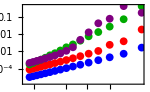

```mathematica
pltSpectrumRelInset=ListLogLogPlot[
{
Table[{1/#dmax,(#μVec[[1]])/(m1Integrability*E8Spectrum[[1]])-1}&@computeLCTSigma[dmax],{dmax,6,36,2}],
Table[{1/#dmax,(#μVec[[2]])/(m1Integrability*E8Spectrum[[2]])-1}&@computeLCTSigma[dmax],{dmax,6,36,2}],
Table[{1/#dmax,(#μVec[[3]])/(m1Integrability*E8Spectrum[[3]])-1}&@computeLCTSigma[dmax],{dmax,6,36,2}],
Table[{1/#dmax,-1+(#μVec[[1]])/(m1Integrability*E8Spectrum[[4]])TakeSmallestBy[Select[(#μVec[[;;]])/(#μVec[[1]]),#>=E8Spectrum[[4]]&],Abs[#-E8Spectrum[[4]]]&,1][[1]]}&@computeLCTSigma[dmax],{dmax,6,36,2}]
},
(*PlotRange->{{0,1/4},Automatic},*)
PlotStyle->{Blue,Red,Darker@Green,Purple},
(*PlotLabel->"relative error",*)
Frame->True,
(*FrameTicks->{None,Automatic},*)
(*FrameLabel->{"1/Δ_max","relative error"},*)
ImageSize->150,
LabelStyle->{Black,FontFamily->"Times New Roman",FontSize->10},
PlotMarkers->{"●",8},
FrameTicks->{Automatic,{
Join[
{#,#,0.03}&/@Range[0.05,0.15,0.05],
{#,"",0.02}&/@Range[0.01,0.15,0.01]
],
None}}
]
```

```mathematica
pltLCTSigmaSpectrum=Show[
Plot[
m1Integrability*{E8Spectrum[[1]],E8Spectrum[[2]],E8Spectrum[[3]],E8Spectrum[[4]]}//Evaluate,
{x,0,1/4},
PlotStyle->(Directive[#,Thickness[0.002]]&/@{Blue,Red,Darker@Green,Purple})
(*PlotStyle->Insert[(Directive[#]&/@{Blue,Red,(*Black,*)Darker@Green}),
Directive[Black,Dashed],3
]*)
],
ListPlot[
{
Table[{1/#dmax,#μVec[[1]]}&@computeLCTSigma[dmax],{dmax,6,36,2}],
Table[{1/#dmax,#μVec[[2]]}&@computeLCTSigma[dmax],{dmax,6,36,2}],
Table[{1/#dmax,#μVec[[3]]}&@computeLCTSigma[dmax],{dmax,6,36,2}],
Flatten[Table[Thread[{1/#dmax,#μVec[[4;;]]}]&@computeLCTSigma[dmax],{dmax,6,36,2}],1],
Table[{1/#dmax,#μVec[[1]]*TakeSmallestBy[Select[(#μVec[[;;]])/(#μVec[[1]]),#>=E8Spectrum[[4]]&],Abs[#-E8Spectrum[[4]]]&,1][[1]]}&@computeLCTSigma[dmax],{dmax,6,36,2}]
},
PlotStyle->{Blue,Red,Darker@Green,Gray,Purple},
PlotMarkers->{"●",7}
],
Axes->False,
PlotRange->{{0,1/5},{0.8,3}*m1Integrability},
Frame->True,
FrameLabel->{Row[{1,"/",Subscript[Δ, max]}],Subscript[m, i]},
ImageSize->450,
LabelStyle->{Black,FontFamily->"Times New Roman",FontSize->12},
Epilog->{ 
Inset[
Framed[PointLegend[
{Blue,Red,Darker@Green,Purple},
Subscript[m, #]&/@Range[4],
LabelStyle->{Black,FontFamily->"Times New Roman",FontSize->12}
],FrameMargins->None,Background->White],
Scaled[{.9,.32}]
],
Inset[
Framed[pltSpectrumRelInset,FrameStyle->Opacity[0],Background->(Blend[{Gray,White},0.95])],Scaled[{.803,.82}]
]
}
]
```

-Graphics-

```mathematica
(*pltLCTSigmaCFunc=ListPlot[
Prepend[
Thread[{#μVec,#cVec//Accumulate}]&@computeLCTSigma[36],
{0,0}
],
InterpolationOrder->0,
PlotStyle->Blue,
Joined->True,
PlotRange->{{0,20},{0.47,0.501}},
Frame->True,
ImageSize->400,
FrameStyle->Black,
LabelStyle->{12,FontFamily->"Times New Roman",Black},
FrameLabel->{Row[{μ,"/",Subscript[m, gap]}],c[μ]}
]*)
```

```mathematica
maxIndexBy[l_,f_] := SortBy[
    Transpose[{l,Range[Length[l]]}],
    -N[f[First[#]]]&][[1,2]];
```

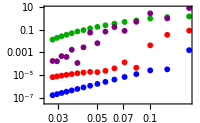

```mathematica
pltCFuncInsetLogLogError=ListLogLogPlot[

{
Table[{1/#dmax,(#cVec[[1]]-ΔCi[[1]])/ΔCi[[1]]//Abs}&@computeLCTSigma[dmax],{dmax,6,36,2}],
Table[{1/#dmax,(#cVec[[2]]-ΔCi[[2]])/ΔCi[[2]]//Abs}&@computeLCTSigma[dmax],{dmax,6,36,2}],
Table[{1/#dmax,(#cVec[[3]]-ΔCi[[3]])/ΔCi[[3]]//Abs}&@computeLCTSigma[dmax],{dmax,6,36,2}],
Table[{1/#dmax,#cVec[[
maxIndexBy[(#μVec[[;;]])/(#μVec[[1]]),-Abs[#-E8Spectrum[[4]]]+If[#<E8Spectrum[[4]],-100,0]&]
]]/ΔCi[[4]]-1//Abs
}&@computeLCTSigma[dmax],{dmax,6,36,2}]
},
PlotStyle->{Blue,Red,Darker@Green,Purple},
PlotMarkers->{{"●",6}},
(*PlotLabel->"relative error",*)
Frame->True,
FrameLabel->{"1/Δ_max","relative error"},
ImageSize->200,
LabelStyle->{Black,FontFamily->"Times New Roman",FontSize->12},
FrameTicks->{Automatic,{
Join[
{#,#,0.03}&/@Range[0.05,0.15,0.05],
{#,"",0.02}&/@Range[0.01,0.15,0.01]
],
None}}
]
```

```mathematica
pltLCTSigmaCFuncBoundState=ListPlot[
{
Table[{1/#dmax,(#cVec[[1]])/ΔCi[[1]]}&@computeLCTSigma[dmax],{dmax,6,36,2}],
Table[{1/#dmax,(#cVec[[2]])/ΔCi[[2]]}&@computeLCTSigma[dmax],{dmax,6,36,2}],
Table[{1/#dmax,(#cVec[[3]])/ΔCi[[3]]}&@computeLCTSigma[dmax],{dmax,6,36,2}],
Table[{1/#dmax,#cVec[[
maxIndexBy[(#μVec[[;;]])/(#μVec[[1]]),-Abs[#-E8Spectrum[[4]]]+If[#<E8Spectrum[[4]],-100,0]&]
]]/ΔCi[[4]]
}&@computeLCTSigma[dmax],{dmax,6,36,2}]
},
PlotRange->{Automatic,{0.901,1.6}},
PlotStyle->{Blue,Red,Darker@Green,Purple},
(*PlotLabel->"relative error",*)
Frame->True,
FrameLabel->{"1/Δ_max",Row[{Subscript[c, i]," / ",Subscript[c, i]^theory}]},
ImageSize->450,
LabelStyle->{Black,FontFamily->"Times New Roman",FontSize->12},
Epilog->{ 
Inset[
Framed[PointLegend[
{Blue,Red,Darker@Green,Purple},
{"c_1","c_2","c_3","c_4"},
LabelStyle->{Black,FontFamily->"Times New Roman",FontSize->12}
]],
Scaled[{.2,.76}]
],
Inset[
Framed[pltCFuncInsetLogLogError,Background->White,FrameStyle->Opacity[0]],
Scaled[{.72,.7}]
]
}
]
```

-Graphics-

## Eta deformation

### subroutines to shoot for the Goldilocks IR cutoff

```mathematica
ClearAll[compareFirstEval]
compareFirstEval[m_,dmax1_,dmax2_][ξ_]:=Module[
{idx,evals,evecs,data},
data=Table[
idx=Select[dictionary,#[[1]]/2+#[[2]]<=dmax&]//Keys;
{evals,evecs}=Eigensystem[(sigmaMatD36[[idx,idx]]+m^2(N@massMatsD36["massFinite"][[idx,idx]]+(2Log[dmax]+ξ)N@massMatsD36["massSingular"][[idx,idx]])),
-4
]//Transpose//SortBy[First]//Transpose;
evals[[1]],
{dmax,{dmax1,dmax2}}
];
(*data//Print;*)
Subtract@@data
]
```

```mathematica
ClearAll[shoot]
shoot[fn_,{x0_,y0_},{x1_,y1_},eps_]:=Module[
{xNew=(x1 y0-x0 y1)/(y0-y1),yNew},
yNew=fn[xNew];
(*Print[{xNew,yNew}//N];*)
If[
Abs[yNew]<eps,
{xNew,yNew},
shoot[fn,{xNew,yNew},{x0,y0},eps]
]
];
shoot[fn_,x0_,x1_,eps_]:=shoot[fn,{x0,fn[x0]},{x1,fn[x1]},eps];
```

### compute the mass IR regulator (run)

```mathematica
ansatzSmall=Monitor[Table[
{m,shoot[compareFirstEval[m,34,36],4,9,10^-5]}//Flatten,
{m,1/10,2,1/10}
],m];
```

```mathematica
ansatzLarge=Monitor[Table[
{m,shoot[compareFirstEval[m,34,36],4,9,10^-5]}//Flatten,
{m,2+1/2,6,1/10}
],m];
```

```mathematica
ansatzLARGE=Monitor[Table[
{m,shoot[compareFirstEval[m,34,36],4,9,10^-5]}//Flatten,
{m,6+1/8,16,1/8}
],m//N];
```

```mathematica
fct=Interpolation[
Join[ansatzSmall[[;;,{1,2}]],ansatzLarge[[;;,{1,2}]],ansatzLARGE[[;;,{1,2}]]]
]
```

InterpolatingFunction[…]

```mathematica
ClearAll[computeLCT]
computeLCT[m_,dmax_]:=computeLCT[m,dmax]=Module[
{idx,evals,evecs,mp,g=1},
idx=Select[dictionary,#[[1]]/2+#[[2]]<=dmax&]//Keys;
mp=m/√((-sigmaEtaFit[m]2π (*m^(1/8)*))/16)//N;
(*mp//Print;Abort[];*)
{evals,evecs}=Eigensystem[((-sigmaEtaFit[m]2π (*m^(1/8)*))/16 sigmaMatD36+(m^2 massMatsD36["massFinite"]+(2Log[dmax] m^2+If[mp>=8,100 m^2,fct[mp] m^2])massMatsD36["massSingular"]))[[idx,idx]]
]//Transpose//SortBy[First]//Transpose;
<|"m"->m,"μVec"->√evals,"cVec"->Abs[evecs[[;;,1]]]^2/2|>
]
```

### compute spectrum

#### insets

FindFit::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

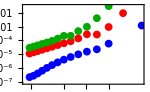

```mathematica
pltEtaDeformConvergenceEtaMinus2Inset=ListLogLogPlot[
Module[
{m=2,pts,fit},
Table[
pts=Table[
{1/dmax,(#μVec[[idx]])/(2m)}&@computeLCT[m,dmax],
{dmax,4+idx*2,34,2}
];
fit=FindFit[pts[[-5;;]],c+a x^b,{a,b,c},x];
MapAt[
(#-c)/c/.fit&,pts,{All,2}
],
{idx,3}
]
],
(*PlotRange->{{0,1/4},Automatic},*)
PlotStyle->{Blue,Red,Darker@Green,Purple},
(*PlotLabel->"relative error",*)
Frame->True,
(*FrameTicks->{None,Automatic},*)
(*FrameLabel->{"1/Δ_max","relative error"},*)
ImageSize->150,
LabelStyle->{Black,FontFamily->"Times New Roman",FontSize->10},
PlotMarkers->{"●",8},
FrameTicks->{Automatic,{
Join[
{#,#,0.03}&/@Range[0.05,0.15,0.05],
{#,"",0.02}&/@Range[0.01,0.15,0.01]
],
None}}
]
```

FindFit::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

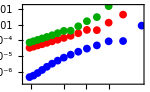

```mathematica
pltEtaDeformConvergenceEtaMinus1Inset=ListLogLogPlot[
Module[
{m=1,pts,fit},
Table[
pts=Table[
{1/dmax,(#μVec[[idx]])/(2m)}&@computeLCT[m,dmax],
{dmax,4+idx*2,34,2}
];
fit=FindFit[pts[[-5;;]],c+a x^b,{a,b,c},x];
MapAt[
(#-c)/c/.fit&,pts,{All,2}
],
{idx,3}
]
],
(*PlotRange->{{0,1/4},Automatic},*)
PlotStyle->{Blue,Red,Darker@Green,Purple},
(*PlotLabel->"relative error",*)
Frame->True,
(*FrameTicks->{None,Automatic},*)
(*FrameLabel->{"1/Δ_max","relative error"},*)
ImageSize->150,
LabelStyle->{Black,FontFamily->"Times New Roman",FontSize->10},
PlotMarkers->{"●",8},
FrameTicks->{Automatic,{
Join[
{#,#,0.03}&/@Range[0.05,0.15,0.05],
{#,"",0.02}&/@Range[0.01,0.15,0.01]
],
None}}
]
```

FindFit::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

General::stop: Further output of FindFit::cvmit will be suppressed during this calculation.

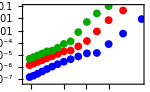

```mathematica
pltEtaDeformConvergenceEtaMinus4Inset=ListLogLogPlot[
Module[
{m=4,pts,fit},
Table[
pts=Table[
{1/dmax,(#μVec[[idx]])/(2m)}&@computeLCT[m,dmax],
{dmax,4+idx*2,34,2}
];
fit=FindFit[pts[[-5;;]],c+a x^b,{a,b,c},x];
MapAt[
(#-c)/c/.fit&,pts,{All,2}
],
{idx,3}
]
],
(*PlotRange->{{0,1/4},Automatic},*)
PlotStyle->{Blue,Red,Darker@Green,Purple},
(*PlotLabel->"relative error",*)
Frame->True,
(*FrameTicks->{None,Automatic},*)
(*FrameLabel->{"1/Δ_max","relative error"},*)
ImageSize->150,
LabelStyle->{Black,FontFamily->"Times New Roman",FontSize->10},
PlotMarkers->{"●",8},
FrameTicks->{Automatic,{
Join[
{#,#,0.03}&/@Range[0.05,0.15,0.05],
{#,"",0.02}&/@Range[0.01,0.15,0.01]
],
None}}
]
```

#### main plots

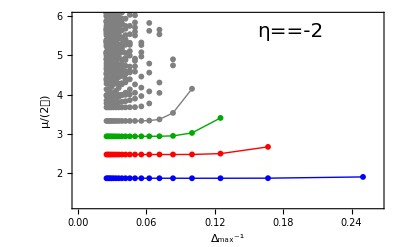

```mathematica
pltEtaDeformConvergenceEtaMinus2=Module[
{m=2,sty=Sequence[{FontFamily->"Times New Roman",FontSize->#,Black}]&},
ListPlot[
{
Table[
{1/dmax,(#μVec[[1]])/(2m)}&@computeLCT[m,dmax],
{dmax,4,40,2}
],
Table[
{1/dmax,(#μVec[[2]])/(2m)}&@computeLCT[m,dmax],
{dmax,6,40,2}
],
Table[
{1/dmax,(#μVec[[3]])/(2m)}&@computeLCT[m,dmax],
{dmax,8,40,2}
],
Table[
{1/dmax,(#μVec[[4]])/(2m)}&@computeLCT[m,dmax],
{dmax,10,40,2}
],
Select[Flatten[Table[
{1/dmax,(#μVec[[5;;]])/(2m)}&@computeLCT[m,dmax]//Thread,
{dmax,10,40,2}
],1],#[[2]]<=50&]
},
(*PlotRange->{{0,1/13.8^6},{0,6}},*)
PlotRange->{{0,1/3.8},{1.2,6}},
PlotStyle->(
Directive[#,Thin]&/@{Blue,Red,Darker@Green,Gray,Gray}
),
Joined->{True,True,True,True,False},
PlotMarkers->{"●",6},
ImageSize->400,
Frame->True,
FrameStyle->Black,
FrameLabel->{Subsuperscript[Δ,max,-1],Row[{μ,"/","(",2,𝓂,")"}]},
LabelStyle->{sty[14]},
Epilog->{
Text[Style[η==-m,sty[20]],Scaled[{.7,.9}]],
Inset[
pltEtaDeformConvergenceEtaMinus2Inset, 
Scaled[{.73,.6}]
]
}
(*FrameTicks->{
{Automatic,None},
{
Thread[{
{1/24,1/20,1/18,1/16,1/14}^6,
Superscript[#,-6]&/@{24,20,18,16,14}
}]
,None}
}*)
]
]
```

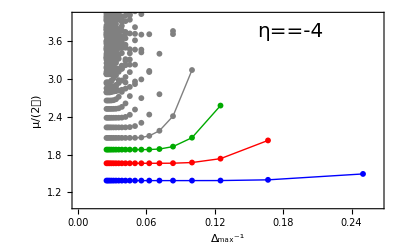

```mathematica
pltEtaDeformConvergenceEtaMinus4=Module[
{m=4,sty=Sequence[{FontFamily->"Times New Roman",FontSize->#,Black}]&},
ListPlot[
{
Table[
{1/dmax,(#μVec[[1]])/(2m)}&@computeLCT[m,dmax],
{dmax,4,40,2}
],
Table[
{1/dmax,(#μVec[[2]])/(2m)}&@computeLCT[m,dmax],
{dmax,6,40,2}
],
Table[
{1/dmax,(#μVec[[3]])/(2m)}&@computeLCT[m,dmax],
{dmax,8,40,2}
],
Table[
{1/dmax,(#μVec[[4]])/(2m)}&@computeLCT[m,dmax],
{dmax,10,40,2}
],
Select[Flatten[Table[
{1/dmax,(#μVec[[5;;]])/(2m)}&@computeLCT[m,dmax]//Thread,
{dmax,10,40,2}
],1],#[[2]]<=50&]
},
(*PlotRange->{{0,1/13.8^6},{0,6}},*)
PlotRange->{{0,1/3.8},{1,4}},
PlotStyle->(
Directive[#,Thin]&/@{Blue,Red,Darker@Green,Gray,Gray}
),
Joined->{True,True,True,True,False},
PlotMarkers->{"●",6},
ImageSize->400,
Frame->True,
FrameStyle->Black,
FrameLabel->{Subsuperscript[Δ,max,-1],Row[{μ,"/","(",2,𝓂,")"}]},
LabelStyle->{sty[14]},
Epilog->{
Text[Style[η==-m,sty[20]],Scaled[{.7,.9}]],
Inset[
pltEtaDeformConvergenceEtaMinus4Inset, 
Scaled[{.73,.6}]
]
}
]
]
```

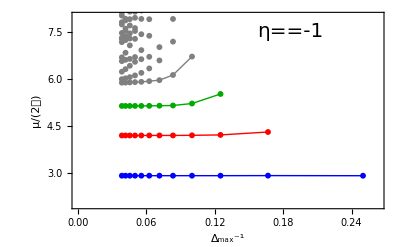

```mathematica
pltEtaDeformConvergenceEtaMinus1=Module[
{m=1,sty=Sequence[{FontFamily->"Times New Roman",FontSize->#,Black}]&},
ListPlot[
{
Table[
{1/dmax,(#μVec[[1]])/(2m)}&@computeLCT[m,dmax],
{dmax,4,26,2}
],
Table[
{1/dmax,(#μVec[[2]])/(2m)}&@computeLCT[m,dmax],
{dmax,6,26,2}
],
Table[
{1/dmax,(#μVec[[3]])/(2m)}&@computeLCT[m,dmax],
{dmax,8,26,2}
],
Table[
{1/dmax,(#μVec[[4]])/(2m)}&@computeLCT[m,dmax],
{dmax,10,26,2}
],
Select[Flatten[Table[
{1/dmax,(#μVec[[5;;]])/(2m)}&@computeLCT[m,dmax]//Thread,
{dmax,10,26,2}
],1],#[[2]]<=50&]
},
(*PlotRange->{{0,1/13.8^6},{0,6}},*)
PlotRange->{{0,1/3.8},{2,8}},
PlotStyle->(
Directive[#,Thin]&/@{Blue,Red,Darker@Green,Gray,Gray}
),
Joined->{True,True,True,True,False},
PlotMarkers->{"●",6},
ImageSize->400,
Frame->True,
FrameStyle->Black,
FrameLabel->{Subsuperscript[Δ,max,-1],Row[{μ,"/","(",2,𝓂,")"}]},
LabelStyle->{sty[14]},
Epilog->{
Text[Style[η==-m,sty[20]],Scaled[{.7,.9}]],
Inset[
pltEtaDeformConvergenceEtaMinus1Inset, 
Scaled[{.73,.6}]
]
}
]
]
```

```mathematica
dataMassAndC2Relative=Monitor[Module[
{idx,evals,evecs,dmax=36},
Table[
Thread[{m,(#μVec)/(#μVec[[1]]),#cVec}]&@computeLCT[m,dmax],
{m,1/10,16,1/10}
]//Transpose
],m//N];
```

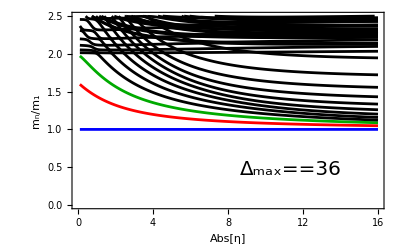

```mathematica
pltEtaDeformAllEvals=ListPlot[
Thread[{#[[;;,1]],#[[;;,2]]}]&/@dataMassAndC2Relative[[;;40]],
PlotStyle->Table[Switch[i,
1,Blue,
2,Red,
3,Darker@Green,
_,Black
],{i,40}],
Joined->True,
PlotRange->{0,2.5},
Frame->True,
ImageSize->400,
Frame->True,
FrameLabel->{Abs[η],Row[{Subscript[m, n],"/",Subscript[m, 1]}]},
LabelStyle->{FontFamily->Times,16,Black},
Epilog->{
Text[Style[Subscript[Δ, max]==36,{FontFamily->Times,20,Black}],Scaled[{.7,.2}]]
}
]
```

### bound states’ central charge contribution

```mathematica
dataMassAndCRescale=Module[
{idx,evals,evecs,mp,dmax=36,g=1},
Table[
idx=Select[dictionary,#[[1]]/2+#[[2]]<=dmax&]//Keys;
mp=m/√((-sigmaEtaFit[m]2π (*m^(1/8)*))/16.019)//N;
(*mp//Print;Abort[];*)
{evals,evecs}=Eigensystem[((-sigmaEtaFit[m]2π (*m^(1/8)*))/16.019 sigmaMatD36+m^2(massMatsD36["massFinite"]+(2Log[dmax]+If[mp>=8,100,fct[mp]])massMatsD36["massSingular"]))[[idx,idx]]
]//Transpose//SortBy[First]//Transpose;
Thread[{m,√evals,Abs[evecs[[;;,1]]]^2/2}],
{m,1/10,18,1/10}
]//Transpose
];
```

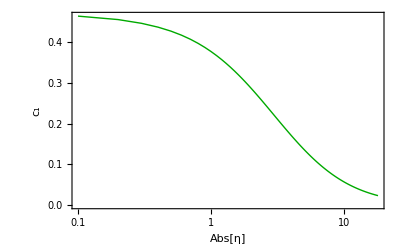

```mathematica
pltIsingLCTWithVevC1=ListLogLinearPlot[
{
Thread[{dataMassAndCRescale[[2,;;,1]],dataMassAndCRescale[[1,;;,3]]}]
},
PlotRange->{{0.1,Automatic},All},
FrameLabel->{Abs[η],Subscript[c, 1]},
Frame->True,
Joined->True,
PlotStyle->{
Directive[Thick,Darker@Green], 
(*Darker@Green,*)
Directive[Thick,Blue,Dashing[0.02]],
Directive[Thickness[0.008],Red,Dashing[0.008]]
},
ImageSize->400,
Frame->True,
FrameStyle->Black,
LabelStyle->{Black,FontFamily->"Times New Roman",FontSize->14}
]
```

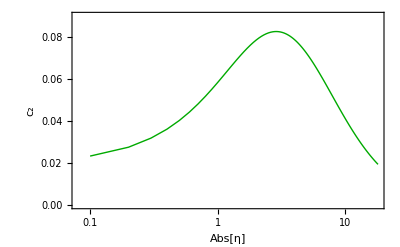

```mathematica
pltIsingLCTWithVevC2=ListLogLinearPlot[
{
Thread[{dataMassAndCRescale[[2,;;,1]],dataMassAndCRescale[[2,;;,3]]}]
},
PlotRange->{0,0.09},
FrameLabel->{Abs[η],Subscript[c, 2]},
Frame->True,
Joined->True,
PlotStyle->{
Directive[Thick,Darker@Green], 
(*Darker@Green,*)
Directive[Thick,Blue,Dashing[0.02]],
Directive[Thickness[0.008],Red,Dashing[0.008]]
},
ImageSize->400,
Frame->True,
FrameStyle->Black,
LabelStyle->{Black,FontFamily->"Times New Roman",FontSize->14}
]
```

### compare with Zamolodchikov

```mathematica
dataMassAndCRescaleLow=Module[
{idx,evals,evecs,mp,dmax=14,g=1},
Table[
idx=Select[dictionary,#[[1]]/2+#[[2]]<=dmax&]//Keys;
mp=m/√((-sigmaEtaFit[m]2π (*m^(1/8)*))/16.019)//N;
(*mp//Print;Abort[];*)
{evals,evecs}=Eigensystem[((-sigmaEtaFit[m]2π (*m^(1/8)*))/16.019 sigmaMatD36+m^2(massMatsD36["massFinite"]+(2Log[dmax]+If[mp>=8,100,fct[mp]])massMatsD36["massSingular"]))[[idx,idx]]
]//Transpose//SortBy[First]//Transpose;
Thread[{m,√evals,Abs[evecs[[;;,1]]]^2/2}],
{m,1/10,4.2//Rationalize,1/10}
]//Transpose
];
```

```mathematica
dataZamolodchikovTFFSA2001[[1,;;,1]]
```

{-0.963855,-0.0803213,-4.24096,-4.21954,-4.19813,-4.17671,-4.15529,-4.13565,-4.11423,-4.09282,-4.0714,-4.04998,-4.02856,-4.00714,-3.98572,-3.96609,-3.94467,-3.92325,-3.90183,-3.88041,-3.85899,-3.83757,-3.81615,-3.79652,-3.7751,-3.75368,-3.73226,-3.71084,-3.68942,-3.66801,-3.64659,-3.62517,-3.60553,-3.58411,-3.5627,-3.54128,-3.51986,-3.49844,-3.47702,-3.4556,-3.43597,-3.41455,-3.39313,-3.37171,-3.35029,-3.32887,-3.30745,-3.28603,-3.2664,-3.24498,-3.22356,-3.20214,-3.18072,-3.1593,-3.13788,-3.11647,-3.09505,-3.07541,-3.05399,-3.03257,-3.01116,-2.98974,-2.96832,-2.9469,-2.92548,-2.90585,-2.88443,-2.86301,-2.84159,-2.82017,-2.79875,-2.77733,-2.75591,-2.73628,-2.71486,-2.69344,-2.67202,-2.6506,-2.62918,-2.60776,-2.58635,-2.56493,-2.54529,-2.52387,-2.50245,-2.48104,-2.45962,-2.4382,-2.41678,-2.39536,-2.37573,-2.35431,-2.33289,-2.31147,-2.29005,-2.26863,-2.24721,-2.22579,-2.20616,-2.18474,-2.16332,-2.1419,-2.12048,-2.09906,-2.07764,-2.05622,-2.03481,-2.01517,-1.99375,-1.97233,-1.95091,-1.9295,-1.90808,-1.88666,-1.86524,-1.8456,-1.82419,-1.80277,-1.78135,-1.75993,-1.73851,-1.71709,-1.69567,-1.67604,-1.65462,-1.6332,-1.61178,-1.59036,-1.56894,-1.54752,-1.5261,-1.50469,-1.48505,-1.46363,-1.44221,-1.42079,-1.39938,-1.37796,-1.35654,-1.33512,-1.31548,-1.29407,-1.27265,-1.25123,-1.22981,-1.20839,-1.18697,-1.16555,-1.14592,-1.1245,-1.10308,-1.08166,-1.06024,-1.03882,-1.0174,-0.995984,-0.974565,-0.954931,-0.933512,-0.912093,-0.890674,-0.869255,-0.847836,-0.826417,-0.804998,-0.785364,-0.763945,-0.742526,-0.721107,-0.699688,-0.678269,-0.65685,-0.635431,-0.615797,-0.594378,-0.572959,-0.551539,-0.53012,-0.508701,-0.487282,-0.465863,-0.444444,-0.42481,-0.403391,-0.381972,-0.360553,-0.339134,-0.317715,-0.296296,-0.274877,-0.255243,-0.233824,-0.212405,-0.190986,-0.169567,-0.148148,-0.126729,-0.10531,-0.085676,-0.0603525,-0.042838,-0.021419,0.,0.021419,0.042838,0.064257,0.085676,0.10531,0.126729,0.148148,0.169567,0.190986,0.212405,0.233824,0.255243,0.274877,0.296296,0.317715,0.339134,0.360553,0.381972,0.403391,0.42481,0.444444,0.465863,0.487282,0.508701,0.53012,0.551539,0.572959,0.594378,0.615797,0.635431,0.65685,0.678269,0.699688,0.721107,0.742526,0.763945,0.785364,0.804998,0.826417,0.847836,0.869255,0.890674,0.912093,0.933512,0.954931,0.974565,0.995984,1.0174,1.03882,1.06024,1.08166,1.10308,1.1245,1.14592,1.16555,1.18697,1.20839,1.22981,1.25123,1.27265,1.29407,1.31548,1.33512,1.35654,1.37796,1.39938,1.42079,1.44221,1.46363,1.48505,1.50469,1.5261,1.54752,1.56894,1.59036,1.61178,1.6332,1.65462,1.67604,1.69567,1.71709,1.73851,1.75993,1.78135,1.80277,1.82419,1.8456,1.86524,1.88666,1.90808,1.9295,1.95091,1.97233,1.99375,2.01517,2.03481,2.05622,2.07764,2.09906,2.12048,2.1419,2.16332,2.18474,2.20616,2.22579,2.24721,2.26863,2.29005,2.31147,2.33289,2.35431,2.37573,2.39536,2.41678,2.4382,2.45962,2.48104,2.50245,2.52387,2.54529,2.56493,2.58635,2.60776,2.62918,2.6506,2.67202,2.69344,2.71486,2.73628,2.75591,2.77733,2.79875,2.82017,2.84159,2.86301,2.88443,2.90585,2.92548,2.9469,2.96832,2.98974,3.01116,3.03257,3.05399,3.07541,3.09505,3.11647,3.13788,3.1593,3.18072,3.20214,3.22356,3.24498,3.2664,3.28603,3.30745,3.32887,3.35029,3.37171,3.39313,3.41455,3.43597,3.4556,3.47702,3.49844,3.51986,3.54128,3.5627,3.58411,3.60553,3.62517,3.64659,3.66801,3.68942,3.71084,3.73226,3.75368,3.7751,3.79652,3.81615,3.83757,3.85899,3.88041,3.90183,3.92325,3.94467,3.96609,3.98572,4.00714,4.02856,4.04998,4.0714,4.09282,4.11423,4.13565,4.15529,4.17671}

```mathematica
legendCompareZamolodchikov=Module[
{sep,size,cols,pix2mm,legends,vals},
sep=0.03; (*separation between the two lines*)
size=0.11; (*thickness of the legends*)

cols={Red,Orange,Black}; (*colours of choice*)
pix2mm=72/25.4; (*pixel to mm conversion*)

(*creates two lines with a given colour,thickness and size.The second line is translated vertically by the variable sep*)
legends={
	Graphics[
		{Directive[Blend[{Blue,Cyan},0.86],Thick],Line[{{{0,0},{10,0}}}]},
		ImageSize->{16*pix2mm,8*pix2mm},
		PlotRangePadding->None
	],
	Show[{
		Graphics[
			{Directive[Red,Dashing[0.2],Thick],Line[{{{0,0},{0.1,0}}}]},
			ImageSize->16*pix2mm
		],
		Graphics[
			{Directive[Pink,Dashing[0.1],Thick],Line[{{{0,-sep},{0.1,-sep}}}]},
			ImageSize->16*pix2mm
		]
	}]
};
(*creating the string associated with each'legend'*)
vals={
Style["TFFSA data",Black,18,FontFamily->"Times New Roman"],
Style[Row[{"LCT ",Subscript[Δ, max]==14,"\n(16 states)"}],Black,18,FontFamily->"Times New Roman"]
};

(*Assembling the two using Grid*)
Grid[{legends[[#]],vals[[#]]}&/@Range@2,Spacings->{1,.7},
Alignment->{Left,Center}
]
]
```

-Graphics- | TFFSA data
-Graphics- | LCT Δ_max==14
(16 states)

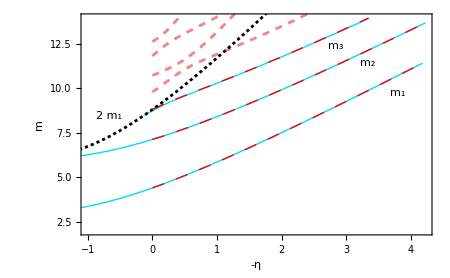

```mathematica
pltCompareZamolodchikov=Show[
ListPlot[
{
dataZamolodchikovTFFSA2001[[1]],
dataZamolodchikovTFFSA2001[[2]],
dataZamolodchikovTFFSA2001[[3]],
Prepend[
Thread[{dataMassAndCRescaleLow[[1,;;,1]],dataMassAndCRescaleLow[[1,;;,2]]}],
{0,computeLCTSigma[14]["μVec"][[1]]}
],
Prepend[
Thread[{dataMassAndCRescaleLow[[2,;;,1]],dataMassAndCRescaleLow[[2,;;,2]]}],
{0,computeLCTSigma[14]["μVec"][[2]]}
],
Prepend[
Thread[{dataMassAndCRescaleLow[[3,;;,1]],dataMassAndCRescaleLow[[3,;;,2]]}],
{0,computeLCTSigma[14]["μVec"][[3]]}
]
},
Joined->True,
PlotStyle->{
Directive[Blend[{Blue,Cyan},0.86],Thick], 
Directive[Blend[{Blue,Cyan},0.86],Thick], 
Directive[Blend[{Blue,Cyan},0.86],Thick], 
Directive[Red,Dashing[0.02],Thick], 
Directive[Red,Dashing[0.02],Thick], 
Directive[Red,Dashing[0.02],Thick]
},
PlotRange->{{-1,All},{2,13.95}}
],
ListPlot[
MapThread[
Prepend,
{
Table[
Thread[{dataMassAndCRescaleLow[[i,;;,1]],dataMassAndCRescaleLow[[i,;;,2]]}],
{i,4,10}
],
{0,#}&/@computeLCTSigma[14]["μVec"][[4;;10]]
}
],
Joined->True,
PlotStyle->Directive[Pink,Dashed](*Directive[Red,Dashing[0.02],Thick]*)
],
ListPlot[
{#[[1]],#[[2]]*2}&/@dataZamolodchikovTFFSA2001[[1]],
Joined->True,
PlotStyle->Directive[Black,Dashing[0.005]]
],
ImageSize->450,
Frame->True,
Axis->{0,0},
FrameStyle->Black,
AxisStyle->Black,
Epilog->{
Black,FontFamily->"Times New Roman",FontSize->20,
Text[Subscript[m, 1],{"3.789","9.731"}],
Text[Subscript[m, 2],{"3.331","11.43"}],
Text[Subscript[m, 3],{"2.836","12.41"}],
Text[2 Subscript[m, 1],{-0.664,8.432}],
Inset[
(*LineLegend[
{
Directive[Blend[{Blue,Cyan},0.86],Thick],
Directive[Red,Dashing[0.02],Thick]
},
{
"TFFSA data",
Row[{"LCT ",Subscript[Δ, max]==14,"\n(16 states)"}]
},
LabelStyle->{Black,FontFamily->"Times New Roman",FontSize->18}
]*)
legendCompareZamolodchikov,
Scaled[{.7,.2}]
]
},
LabelStyle->{Black,FontFamily->"Times New Roman",FontSize->14},
FrameLabel->{-η,m}
]
```

## compare LCT with perturbative at large eta

```mathematica
sigmaBarInf=1.35783834170660;
```

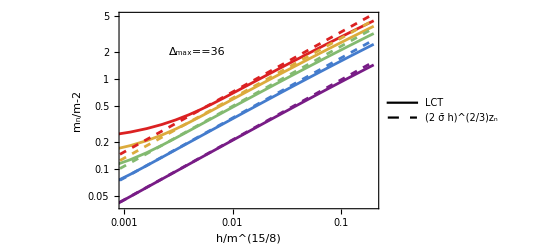

```mathematica
pltLCTEtaInf36=Module[
{idx,evals,evecs,dmax=36,m1=1,nmax=5,
pts,
sty=Sequence@@{Black,FontFamily->"Times New Roman",FontSize->#}&
},
pts=Table[
idx=Select[dictionary,#[[1]]/2+#[[2]]<=dmax&]//Keys;
{evals,evecs}=Eigensystem[(2π h*(sigmaBarInf/16.019) sigmaMatD36+m1^2(massMatsD36["massFinite"]+(2Log[dmax]+1000)massMatsD36["massSingular"]))[[idx,idx]]
]//Transpose//SortBy[First]//Transpose;
Thread[{h,√evals-2(*Abs[evecs[[;;,1]]]^2/2*)}][[;;nmax]],
{h,1/5*Subdivide[0,1,40]^4}
]//Transpose;
Show[
ListLogLogPlot[
pts,
Joined->True,
PlotStyle->(Directive[ColorData["Rainbow"][#]]&/@Subdivide[0,1,nmax-1]),
PlotRange->{{0.001,0.2},{0.04,5}}
],
LogLogPlot[
Table[
(-AiryAiZero[n])*(2sigmaBarInf h)^(2/3),
{n,1,nmax}
]//Evaluate,
{h,0,1/5},
PlotStyle->(Directive[ColorData["Rainbow"][#],Dashed]&/@Subdivide[0,1,nmax-1])
],
ImageSize->400,
Frame->True,
FrameLabel->{Row[{h,"/",Superscript[m,"15/8"]}],Row[{Subscript[m, n],"/",m,-2}]},
LabelStyle->{sty[14]},
BaseStyle->{sty[14]},
Epilog->{
Inset[
LineLegend[
{Directive[Black],Directive[Black,Dashed]},
{
(*MaTeX["g_{\\rm eff}=g^2\\frac{\\langle\\sigma(R\\gg 1)\\rangle}{\\langle\\sigma(R\\ll 1)\\rangle}",
FontSize->14]*)
LCT,
RowBox[{
SuperscriptBox[RowBox[{"(",2,OverBar[σ],h,")"}],2/3],
SubscriptBox[z,n]
}]//DisplayForm
},
LabelStyle->{sty[14]}
],
Scaled[{.72,.23}]
], 
Text[Subscript[Δ, max]==36,Scaled[{.3,.8}]]
}
]
]
```

## Form factors from Integrability

## define

```mathematica
ClearAll[GMixed]
GMixed[λ_,Ntrunc_,prec_,NSample_]:=GMixed[λ,Ntrunc,prec,NSample]=Module[
{θh,out,data,fit},
data=Table[
θh=ⅈ π-θ;
out=Product[
(((1+((θh/(2π))/(k+1-λ/2))^2)(1+((θh/(2π))/(k+1/2+λ/2))^2))/((1+((θh/(2π))/(k+1+λ/2))^2)(1+((θh/(2π))/(k+3/2-λ/2))^2)))^(k+1),
{k,0,Ntrunc-1}
]*SetPrecision[Exp[NIntegrate[
2/(x Log[x])(2 x^(1-λ) (x+x^(2 λ)))/((-1+x) (1+x)^2)((1+Ntrunc-Ntrunc/x^2) x^(-2 Ntrunc))(1/2 ⅈ x^(-(ⅈ θh)/(2 π))-1/2 ⅈ x^((ⅈ θh)/(2 π)))^2,
{x,1,Infinity},
WorkingPrecision->prec,
MaxRecursion->20
]],prec]/Exp[Abs[θ]/2];
{If[θ>500,0,Exp[-θ]],out},
{θ,Sinh[Round[Subdivide[0,Log[NSample],NSample],NSample^-4]]
(*Sinh[Sinh[Subdivide[0,Log[NSample],NSample]]]*)~Join~{1000}}
];
(*fit=Evaluate[Fit[data,#^Range[0,NSample/2//Floor],# ]]&;*)
fit=Evaluate[Interpolation[SetPrecision[data,prec],InterpolationOrder->5][Exp[-#]]]&;
With[
{func=fit},
Switch[
#,_?NonNegative,fit[#]Exp[Abs[#]/2],_?Negative,-Tanh[1/2(#+ⅈ π λ)]/Tanh[1/2(#-ⅈ π λ)]fit[-#]Exp[Abs[#]/2]
]&
]
(*Evaluate[fit[-Log[#]]]&*)
(*data//Print;*)
(*Interpolation[SetPrecision[data,prec],InterpolationOrder->5]*)
]
```

```mathematica
amplitude=<|
{1,1}->{20,12,2},
{1,2}->{24,18,14,8},
{1,3}->{29,21,13,3,11,11},
{2,2}->{24,20,14,8,2,12,12},
{2,3}->{25,19,9,7,7,13,13,15},
{3,3}->{22,20,20,20,14,12,12,12,4,2,2},
{1,4}->{23,21,17,11,7,15},
{1,5}->{28,22,14,4,10,10,12,12}
|>/30
```

<|{1,1}→{2/3,2/5,1/15},{1,2}→{4/5,3/5,7/15,4/15},{1,3}→{29/30,7/10,13/30,1/10,11/30,11/30},{2,2}→{4/5,2/3,7/15,4/15,1/15,2/5,2/5},{2,3}→{5/6,19/30,3/10,7/30,7/30,13/30,13/30,1/2},{3,3}→{11/15,2/3,2/3,2/3,7/15,2/5,2/5,2/5,2/15,1/15,1/15},{1,4}→{23/30,7/10,17/30,11/30,7/30,1/2},{1,5}→{14/15,11/15,7/15,2/15,1/3,1/3,2/5,2/5}|>

```mathematica
fMin[Ntrunc_,prec_,NSample_][a_,b_]:=Evaluate[
(-ⅈ Sinh[1/2#])^KroneckerDelta[a,b]*
Product[
GMixed[α,Ntrunc,prec,NSample][#],
{α,amplitude[{a,b}]}
]]&
```

```mathematica
polyCoeffData=<|
{1,1}-><|
1->1.623628945,
0->7.906814252
|>,
{1,2}-><|
1->6.189362113,
0->48.76949783
|>,
{1,3}-><|
2->451.6582994,
1->4824.093743,
0->4389.138083
|>,
{1,3}-><|
2->451.6582994,
1->4824.093743,
0->4389.138083
|>,
{2,2}-><|
3->16.66647213,
2->258.9398602,
1->613.8726746,
0->388.0488792
|>,
{1,4}-><|
2->−17.51368456,
1->−222.5261059,
0->-207.6061104
|>,
{2,3}-><|
3->71.93457181,
2->1358.926475,
1->3745.854658,
0->2718.541527
|>,
{1,5}-><|
3->202.2760111,
2->3328.024309,
1->6286.863589,
0->3162.939632
|>,
{3,3}-><|
5->928.5620526,
4->23400.66614,
3->116753.1311,
2->233559.8778,
1->207377.6722,
0->68123.67968
|>
|>;
```

```mathematica
𝒫[α_,θ_]:=(Cos[π α]-Cosh[θ])/(2 Cos[π α/2]^2);
polesD[a_,b_,θ_]:=Module[
{counts=Counts[amplitude[{a,b}]],n },
Product[
n=counts[α];
𝒫[α,θ]^Floor[(n+1)/2] 𝒫[1-α,θ]^Floor[n/2],
{α,counts//Keys}
]
]
residuesQ[a_,b_,θ_]:=Module[
{m=E8Spectrum},
(Cosh[θ]+(m[[a]]^2+m[[b]]^2)/(2m[[a]]m[[b]]))^(1-KroneckerDelta[a,b])*
polyP[a,b,θ]
];
polyP[a_,b_,θ_]:=KeyValueMap[
#2 Cosh[θ]^#1&,
polyCoeffData[{a,b}]
]//Total
```

```mathematica
fSig[Ntrunc_,prec_,NSample_][a_,b_,θ_]:=residuesQ[a,b,θ]/polesD[a,b,θ] fMin[Ntrunc,prec,NSample][a,b][θ]
```

```mathematica
ClearAll[GMixedDirect]
GMixedDirect[λ_,Ntrunc_,prec_,θ_]:=GMixedDirect[λ,Ntrunc,prec,θ]=Module[
{θh,out,data,fit},
θh=ⅈ π-θ;Product[
(((1+((θh/(2π))/(k+1-λ/2))^2)(1+((θh/(2π))/(k+1/2+λ/2))^2))/((1+((θh/(2π))/(k+1+λ/2))^2)(1+((θh/(2π))/(k+3/2-λ/2))^2)))^(k+1),
{k,0,Ntrunc-1}
]*SetPrecision[Exp[NIntegrate[
2/(x Log[x])(2 x^(1-λ) (x+x^(2 λ)))/((-1+x) (1+x)^2)((1+Ntrunc-Ntrunc/x^2) x^(-2 Ntrunc))(1/2 ⅈ x^(-(ⅈ θh)/(2 π))-1/2 ⅈ x^((ⅈ θh)/(2 π)))^2,
{x,1,Infinity},
WorkingPrecision->prec,
MaxRecursion->20
]],prec]
]
```

```mathematica
fMinDirect[Ntrunc_,prec_][a_,b_,θ_]:=
(-ⅈ Sinh[1/2 θ])^KroneckerDelta[a,b]*
Product[
GMixedDirect[α,Ntrunc,prec,θ],
{α,amplitude[{a,b}]}
]
```

```mathematica
fSigDirect[Ntrunc_,prec_][a_,b_,θ_]:=residuesQ[a,b,θ]/polesD[a,b,θ] fMinDirect[Ntrunc,prec][a,b,θ]
```

## Run

```mathematica
(*dataΘIntDensityTheoretical=Module[
{m=E8Spectrum},
Table[
{μ,(*Total[ΔCi[[;;3]]*E8Spectrum[[;;3]]^4/4]+*)Sum[
If[μ<m[[ab[[1]]]]+m[[ab[[2]]]],0,
(2-KroneckerDelta@@ab)3/4 1/(2 π^2)NIntegrate[
(*(2π(2-2*1/8))^2*)(*4/((m[[ab[[1]]]]^2+m[[ab[[2]]]]^2+2m[[ab[[1]]]]m[[ab[[2]]]]Cosh[θ1])^2)*)Abs[fSig[100,100,100][ab[[1]],ab[[2]],θ1]]^2,
{θ1,-ArcCosh[(μ^2-m[[ab[[1]]]]^2-m[[ab[[2]]]]^2)/(2m[[ab[[1]]]]m[[ab[[2]]]])],ArcCosh[(μ^2-m[[ab[[1]]]]^2-m[[ab[[2]]]]^2)/(2m[[ab[[1]]]]m[[ab[[2]]]])]}
]
],
{ab,Keys[amplitude]}
]+Total[HeavisideTheta[μ-Round[E8Spectrum,10^-6]]*ΔCi*E8Spectrum^4/4]
},
{μ,Select[Join[
Subdivide[0,4,41],
Round[E8Spectrum[[;;]],10^-6]+10^-5,
Round[E8Spectrum[[;;]],10^-6]-10^-5
]//Sort,#<=4&]}
]
];//AbsoluteTiming*)
```

```mathematica
(*dataΘIntDensityTheoretical={{0,0.},{4/41,0.},{8/41,0.},{12/41,0.},{16/41,0.},{20/41,0.},{24/41,0.},{28/41,0.},{32/41,0.},{36/41,0.},{40/41,0.},{99999/100000,0.},{100001/100000,0.11800957049575288},{44/41,0.11800957049575288},{48/41,0.11800957049575288},{52/41,0.11800957049575288},{56/41,0.11800957049575288},{60/41,0.11800957049575288},{64/41,0.11800957049575288},{202253/125000,0.11800957049575288},{404511/250000,0.1509628379649326},{68/41,0.1509628379649326},{72/41,0.1509628379649326},{76/41,0.1509628379649326},{80/41,0.1509628379649326},{994517/500000,0.1509628379649326},{994527/500000,0.16096951742495963},{84/41,0.1641411729935068},{88/41,0.16860751265734575},{92/41,0.17185657181776365},{96/41,0.1744839624792547},{2404857/1000000,0.17596562329273108},{2404877/1000000,0.18182230226372362},{100/41,0.18256206237926803},{104/41,0.1844898141417902},{108/41,0.1877289849855398},{112/41,0.19214940056552451},{116/41,0.19544898943095584},{120/41,0.19829135948598386},{591257/200000,0.1990836748923504},{591261/200000,0.2001297515724521},{124/41,0.20212574960137952},{128/41,0.20501557382025182},{321833/100000,0.2075721540610975},{64367/20000,0.2081135388693553},{132/41,0.2081428745969212},{136/41,0.2107051457544603},{140/41,0.21397687542929647},{144/41,0.2183247463953391},{148/41,0.22165483193776703},{152/41,0.2247427716682827},{156/41,0.22752028809111763},{3891147/1000000,0.22979776544897887},{3891167/1000000,0.2298757905817909},{160/41,0.23016256925285586},{4,0.23257780550864815}};*)
```

```mathematica
(*dataΘIntDensityTheoreticalIntp=Interpolation[dataΘIntDensityTheoretical,InterpolationOrder->1]*)
```

```mathematica
dataΘIntDensityTheoreticalIntp=InterpolatingFunction[…];
```

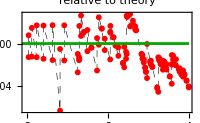

```mathematica
pltΘIntDensityRelative=Show[ListPlot[
{
{#[[1]],#[[2]]-dataΘIntDensityTheoreticalIntp[#[[1]]]}&/@Select[
Thread[{((#μVec)/m1Integrability)[[2;;]],((#μVec)^4/(4 m1Integrability^4)#cVec//Accumulate)[[;;-2]]}]&@computeLCTSigma[36],
2<=#[[1]]<=4&
],
{#[[1]],#[[2]]-dataΘIntDensityTheoreticalIntp[#[[1]]]}&/@Select[
Thread[{(#μVec)/m1Integrability,(#μVec)^4/(4 m1Integrability^4)#cVec//Accumulate}]&@computeLCTSigma[36],
2<=#[[1]]<=4&
]
}//Transpose//Flatten[#,1]&//{#,#}&,
InterpolationOrder->{1,0,1},
PlotStyle->{
Directive[Black,Dashed,Thickness[0.002]], 
Red
},
Joined->{True,False},
PlotMarkers->{None,
{"●",6}
},
(*PlotRange->{{2,4},{0,0.3}},*)
PlotLabel->"relative to theory",
Frame->True,
ImageSize->200,
FrameStyle->Black,
LabelStyle->{12,FontFamily->"Times New Roman",Black}
(*FrameLabel->{μ,Subscript[ρ, Θ][μ]}*)
],
Plot[0,{x,0,4},PlotStyle->Darker@Green]
]
```

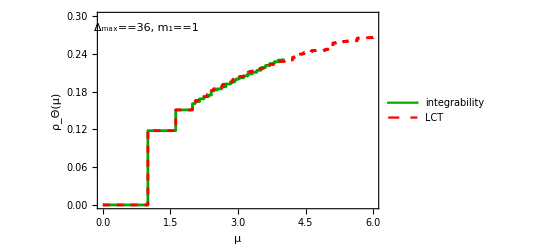

```mathematica
pltΘIntDensity=Module[
{sty=Function[Sequence@@{FontSize->#,FontFamily->"Times New Roman",Black}]},
ListPlot[
{
{#[[1]],#[[2]]}&/@dataΘIntDensityTheoretical,
Prepend[
Thread[{(#μVec)/m1Integrability,(#μVec)^4/(4 m1Integrability^4)#cVec//Accumulate}]&@computeLCTSigma[36],
{0,0}
]
},
InterpolationOrder->{0,0,1},
PlotStyle->{
Darker@Green,
Directive[Red,Dashed]
},
Joined->True,
PlotRange->{{0,6},{0,0.3}},
Frame->True,
ImageSize->400,
FrameStyle->Black,
LabelStyle->{12,FontFamily->"Times New Roman",Black},
BaseStyle->{12,FontFamily->"Times New Roman",Black},
FrameLabel->{μ,Subscript[ρ, Θ][μ]},
Epilog->{
Inset[
pltΘIntDensityRelative,
Scaled[{.7,.32}]
],
Inset[
LineLegend[
{
Darker@Green,
Directive[Red,Dashed]
},
{
"integrability",
"LCT"
},
LabelStyle->{12,FontFamily->"Times New Roman",Black}
],
Scaled[{.22,.7}]
],
sty[12],
Text[Row[{Subscript[Δ, max]==36,", ",Subscript[m, 1]==1}],Scaled[{.175,.92}]]
}
]
]
```

```mathematica
(*dataCFuncTheoretical=Module[
{m=E8Spectrum},
Table[
{μ,(*Total[ΔCi[[;;3]]*E8Spectrum[[;;3]]^4/4]+*)Sum[
If[μ<m[[ab[[1]]]]+m[[ab[[2]]]],0,
(2-KroneckerDelta@@ab)3/4 1/(2 π^2)NIntegrate[
(*(2π(2-2*1/8))^2*)4/((m[[ab[[1]]]]^2+m[[ab[[2]]]]^2+2m[[ab[[1]]]]m[[ab[[2]]]]Cosh[θ1])^2)Abs[fSig[100,100,100][ab[[1]],ab[[2]],θ1]]^2,
{θ1,-ArcCosh[(μ^2-m[[ab[[1]]]]^2-m[[ab[[2]]]]^2)/(2m[[ab[[1]]]]m[[ab[[2]]]])],ArcCosh[(μ^2-m[[ab[[1]]]]^2-m[[ab[[2]]]]^2)/(2m[[ab[[1]]]]m[[ab[[2]]]])]}
]
],
{ab,Keys[amplitude]}
]+Total[HeavisideTheta[μ-Round[E8Spectrum,10^-6]]*ΔCi]
},
{μ,Select[Join[
Subdivide[0,4,41],
Round[E8Spectrum[[;;]],10^-6]+10^-5,
Round[E8Spectrum[[;;]],10^-6]-10^-5
]//Sort,#<=4&]}
]
]*)
```

```mathematica
dataCFuncTheoretical={{0,0.},{4/41,0.},{8/41,0.},{12/41,0.},{16/41,0.},{20/41,0.},{24/41,0.},{28/41,0.},{32/41,0.},{36/41,0.},{40/41,0.},{99999/100000,0.},{100001/100000,0.4720382819830115},{44/41,0.4720382819830115},{48/41,0.4720382819830115},{52/41,0.4720382819830115},{56/41,0.4720382819830115},{60/41,0.4720382819830115},{64/41,0.4720382819830115},{202253/125000,0.4720382819830115},{404511/250000,0.4912695497006177},{68/41,0.4912695497006177},{72/41,0.4912695497006177},{76/41,0.4912695497006177},{80/41,0.4912695497006177},{994517/500000,0.4912695497006177},{994527/500000,0.49382679624943704},{84/41,0.4945830372480801},{88/41,0.49551353671237053},{92/41,0.49607623319982264},{96/41,0.4964581771627942},{2404857/1000000,0.49664531114008237},{2404877/1000000,0.49734571258651605},{100/41,0.497431745586171},{104/41,0.49763365320844527},{108/41,0.49791624197479256},{112/41,0.4982599942169879},{116/41,0.4984814959735021},{120/41,0.49864760499037725},{591257/200000,0.4986899434367201},{591261/200000,0.4987447247347024},{124/41,0.4988443903407382},{128/41,0.4989742607502367},{321833/100000,0.49907569363177406},{64367/20000,0.4990958790669562},{132/41,0.49909697204198966},{136/41,0.49918685658777595},{140/41,0.49928759357984404},{144/41,0.49940914431761557},{148/41,0.49949211375560476},{152/41,0.49956119071394633},{156/41,0.49961708094905416},{3891147/1000000,0.49965866868346115},{3891167/1000000,0.4996600300641011},{160/41,0.4996650049089514},{4,0.49970467282315245}};
```

```mathematica
(*dataCFuncTheoreticalIntp=Interpolation[dataCFuncTheoretical,InterpolationOrder->1]*)
```

```mathematica
dataCFuncTheoreticalIntp=InterpolatingFunction[…];
```

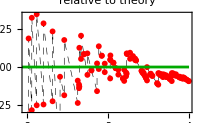

```mathematica
pltCFuncRelative=Show[ListPlot[
{
{#[[1]],#[[2]]-dataCFuncTheoreticalIntp[#[[1]]]}&/@Select[
Thread[{((#μVec)/m1Integrability)[[2;;]],(#cVec//Accumulate)[[;;-2]]}]&@computeLCTSigma[36],
2<=#[[1]]<=4&
],
{#[[1]],#[[2]]-dataCFuncTheoreticalIntp[#[[1]]]}&/@Select[
Thread[{(#μVec)/m1Integrability,#cVec//Accumulate}]&@computeLCTSigma[36],
2<=#[[1]]<=4&
]
}//Transpose//Flatten[#,1]&//{#,#}&,
InterpolationOrder->{1,0,1},
PlotStyle->{
Directive[Black,Dashed,Thickness[0.002]], 
Red
},
Joined->{True,False},
PlotMarkers->{None,
{"●",6}
},
(*PlotRange->{{2,4},{0,0.3}},*)
PlotLabel->"relative to theory",
Frame->True,
ImageSize->200,
FrameStyle->Black,
LabelStyle->{12,FontFamily->"Times New Roman",Black}
(*FrameLabel->{μ,Subscript[ρ, Θ][μ]}*)
],
Plot[0,{x,0,4},PlotStyle->Darker@Green]
]
```

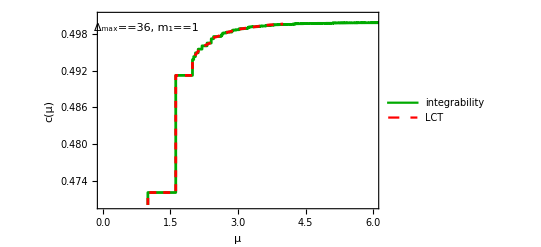

```mathematica
pltLCTSigmaCFunc=Module[
{sty=Function[Sequence@@{FontSize->#,FontFamily->"Times New Roman",Black}]},
ListPlot[
{
Prepend[
Thread[{(#μVec)/m1Integrability,#cVec//Accumulate}]&@computeLCTSigma[36],
{0,0}
],
dataCFuncTheoretical
},
InterpolationOrder->{0,1},
PlotStyle->{
Darker@Green,
Directive[Red,Dashed]
},
Joined->True,
PlotRange->{{0,6},{0.47,0.501}},
Frame->True,
ImageSize->400,
FrameStyle->Black,
LabelStyle->{12,FontFamily->"Times New Roman",Black},
FrameLabel->{μ,c[μ]},
Epilog->{
Inset[
pltCFuncRelative,
Scaled[{.7,.32}]
],
Inset[
LineLegend[
{
Darker@Green,
Directive[Red,Dashed]
},
{
"integrability",
"LCT"
}
],
Scaled[{.7,.75}]
],
sty[12],
Text[Row[{Subscript[Δ, max]==36,", ",Subscript[m, 1]==1}],Scaled[{.175,.92}]]
}
]
]
```

## Form factors from truncation

## define

```mathematica
RegJacobiP[n_,α_,β_,x_]:=0/;n<0;
RegJacobiP[n_,α_,β_,x_]:=JacobiP[n,α,β,x]
```

```mathematica
ClearAll[FFactorsMemoized]
FFactorsMemoized[h1_,h2_,X_]:=FFactorsMemoized[h1,h2,X]=With[{hO=2},
(X^(h1-hO/2)  )RegJacobiP[-1-h1+h2+hO,-1+2 h1,1-2 hO,1-2 X]
];
```

```mathematica
ClearAll[computeLCTSigmaWithEvecs]
computeLCTSigmaWithEvecs[dmax_]:=computeLCTSigmaWithEvecs[dmax]=Module[
{idx,evals,evecs,mp},
idx=Select[dictionary,#[[1]]/2+#[[2]]<=dmax&]//Keys;
(*mp//Print;Abort[];*)
{evals,evecs}=Eigensystem[sigmaMatD36[[idx,idx]]
]//Transpose//SortBy[First]//Transpose;
<|"dmax"->dmax,"μVec"->√(((2π)^(16/15)vecE8*16/15)/16 2π *evals),
"evecs"->evecs[[;;3]],
"cVec"->Abs[evecs[[;;,1]]]^2/2
|>
]
```

## some tests

```mathematica
dataFormFactorLCTInOut11=Module[
{idx=1,evec,m,data},
data=computeLCTSigmaWithEvecs[26];
evec=data["evecs"][[idx]];
m=(data["μVec"][[idx]])/(data["μVec"][[1]]);
Table[
{θ,2π m^2 evec.(Outer[
FFactorsMemoized[#1,#2,Cosh[θ//Abs]-Sinh[θ//Abs]]&,
#[[1]]/2+#[[2]]&/@dictionaryD26//Values,
#[[1]]/2+#[[2]]&/@dictionaryD26//Values
]*tmmMatD26).evec},
{θ,Subdivide[0,3,40]}
]
]
```

{{0,6.28319},{3/40,6.2362},{3/20,6.09819},{9/40,5.87789},{3/10,5.5895},{3/8,5.24678},{9/20,4.86964},{21/40,4.47099},{3/5,4.06603},{27/40,3.6691},{3/4,3.28409},{33/40,2.91873},{9/10,2.58119},{39/40,2.27068},{21/20,1.98424},{9/8,1.72392},{6/5,1.49254},{51/40,1.28788},{27/20,1.10429},{57/40,0.937967},{3/2,0.78893},{63/40,0.658581},{33/20,0.54649},{69/40,0.449512},{9/5,0.363358},{15/8,0.284782},{39/20,0.212706},{81/40,0.147842},{21/10,0.0914304},{87/40,0.04403},{9/4,0.00493745},{93/40,-0.0276561},{12/5,-0.056045},{99/40,-0.0823},{51/20,-0.107762},{21/8,-0.132859},{27/10,-0.157231},{111/40,-0.180027},{57/20,-0.200272},{117/40,-0.21717},{3,-0.230304}}

```mathematica
dataFormFactorLCTInOut22=Module[
{idx=2,evec,m,data},
data=computeLCTSigmaWithEvecs[26];
evec=data["evecs"][[idx]];
m=(data["μVec"][[idx]])/(data["μVec"][[1]]);
Table[
{θ,2π m^2 evec.(Outer[
FFactorsMemoized[#1,#2,Cosh[θ//Abs]-Sinh[θ//Abs]]&,
#[[1]]/2+#[[2]]&/@dictionaryD26//Values,
#[[1]]/2+#[[2]]&/@dictionaryD26//Values
]*tmmMatD26).evec},
{θ,Subdivide[0,3,40]}
]
]
```

{{0,16.4533},{3/40,15.608},{3/20,13.3042},{9/40,10.1318},{3/10,6.77919},{3/8,3.80235},{9/20,1.51245},{21/40,-0.00523494},{3/5,-0.853813},{27/40,-1.17543},{3/4,-1.14099},{33/40,-0.915951},{9/10,-0.606074},{39/40,-0.273725},{21/20,0.0321011},{9/8,0.279217},{6/5,0.461246},{51/40,0.588642},{27/20,0.672916},{57/40,0.720026},{3/2,0.733465},{63/40,0.71883},{33/20,0.684575},{69/40,0.63958},{9/5,0.590513},{15/8,0.540905},{39/20,0.491886},{81/40,0.443538},{21/10,0.395959},{87/40,0.349658},{9/4,0.305447},{93/40,0.264126},{12/5,0.226234},{99/40,0.191954},{51/20,0.161164},{21/8,0.133572},{27/10,0.108836},{111/40,0.0866515},{57/20,0.066787},{117/40,0.0490723},{3,0.0333693}}

```mathematica
dataFormFactorLCTInOut33=Module[
{idx=3,evec,m,data},
data=computeLCTSigmaWithEvecs[26];
evec=data["evecs"][[idx]];
m=(data["μVec"][[idx]])/(data["μVec"][[1]]);
Table[
{θ,2π m^2 evec.(Outer[
FFactorsMemoized[#1,#2,Cosh[θ//Abs]-Sinh[θ//Abs]]&,
#[[1]]/2+#[[2]]&/@dictionaryD26//Values,
#[[1]]/2+#[[2]]&/@dictionaryD26//Values
]*tmmMatD26).evec},
{θ,Subdivide[0,3,80]}
]
]
```

{{0,24.8843},{3/80,23.2614},{3/40,18.8603},{9/80,12.8758},{3/20,6.71856},{3/16,1.54812},{9/40,-2.02329},{21/80,-3.92217},{3/10,-4.43741},{27/80,-4.02258},{3/8,-3.12602},{33/80,-2.08662},{9/20,-1.10949},{39/80,-0.293667},{21/40,0.327905},{9/16,0.758216},{3/5,1.01835},{51/80,1.13695},{27/40,1.14349},{57/80,1.0647},{3/4,0.923784},{63/80,0.741593},{33/40,0.537921},{69/80,0.331717},{9/10,0.140007},{15/16,-0.0238359},{39/40,-0.151532},{81/80,-0.240361},{21/20,-0.292501},{87/80,-0.313537},{9/8,-0.310662},{93/80,-0.291083},{6/5,-0.260929},{99/80,-0.224767},{51/40,-0.185618},{21/16,-0.145284},{27/20,-0.104793},{111/80,-0.0647916},{57/40,-0.0258234},{117/80,0.0115481},{3/2,0.0467281},{123/80,0.0791493},{63/40,0.108351},{129/80,0.134039},{33/20,0.156114},{27/16,0.174659},{69/40,0.18989},{141/80,0.202108},{9/5,0.21163},{147/80,0.218746},{15/8,0.223688},{153/80,0.22662},{39/20,0.227642},{159/80,0.226814},{81/40,0.224179},{33/16,0.21979},{21/10,0.213733},{171/80,0.206144},{87/40,0.197211},{177/80,0.187177},{9/4,0.176328},{183/80,0.164975},{93/40,0.153443},{189/80,0.142047},{12/5,0.131074},{39/16,0.120773},{99/40,0.11134},{201/80,0.102913},{51/20,0.0955708},{207/80,0.0893316},{21/8,0.0841605},{213/80,0.0799765},{27/10,0.0766609},{219/80,0.0740684},{111/40,0.0720363},{45/16,0.0703951},{57/20,0.0689768},{231/80,0.0676225},{117/40,0.0661888},{237/80,0.0645517},{3,0.0626101}}

```mathematica
dataFInOut11=Table[
{x,fSigDirect[100,100][1,1,ⅈ π+x]},
{x,Replace[Subdivide[-3,3,30],0->1/10000,1]}
]
```

{{-3,-0.218188+0. ⅈ},{-14/5,-0.181574+0. ⅈ},{-13/5,-0.131182+0. ⅈ},{-12/5,-0.061504+0. ⅈ},{-11/5,0.0352818+0. ⅈ},{-2,0.170245+0. ⅈ},{-9/5,0.358916+0. ⅈ},{-8/5,0.622635+0. ⅈ},{-7/5,0.989573+0. ⅈ},{-6/5,1.49402+0. ⅈ},{-1,2.1708+0. ⅈ},{-4/5,3.03881+0. ⅈ},{-3/5,4.06678+0. ⅈ},{-2/5,5.12443+0. ⅈ},{-1/5,5.95985+0. ⅈ},{1/10000,6.28319+0. ⅈ},{1/5,5.95985+0. ⅈ},{2/5,5.12443+0. ⅈ},{3/5,4.06678+0. ⅈ},{4/5,3.03881+0. ⅈ},{1,2.1708+0. ⅈ},{6/5,1.49402+0. ⅈ},{7/5,0.989573+0. ⅈ},{8/5,0.622635+0. ⅈ},{9/5,0.358916+0. ⅈ},{2,0.170245+0. ⅈ},{11/5,0.0352818+0. ⅈ},{12/5,-0.061504+0. ⅈ},{13/5,-0.131182+0. ⅈ},{14/5,-0.181574+0. ⅈ},{3,-0.218188+0. ⅈ}}

```mathematica
dataFInOut22=Table[
{x,fSigDirect[100,100][2,2,ⅈ π+x]},
{x,Replace[Subdivide[-3,3,30],0->1/10000,1]}
]
```

{{-3,0.0392609+0. ⅈ},{-14/5,0.0847432+0. ⅈ},{-13/5,0.145951+0. ⅈ},{-12/5,0.227042+0. ⅈ},{-11/5,0.331309+0. ⅈ},{-2,0.457973+0. ⅈ},{-9/5,0.595062+0. ⅈ},{-8/5,0.705778+0. ⅈ},{-7/5,0.708134+0. ⅈ},{-6/5,0.462593+0. ⅈ},{-1,-0.166902+0. ⅈ},{-4/5,-1.00777+0. ⅈ},{-3/5,-0.851536+0. ⅈ},{-2/5,2.95421+0. ⅈ},{-1/5,11.2402+0. ⅈ},{1/10000,16.4496+0. ⅈ},{1/5,11.2402+0. ⅈ},{2/5,2.95421+0. ⅈ},{3/5,-0.851536+0. ⅈ},{4/5,-1.00777+0. ⅈ},{1,-0.166902+0. ⅈ},{6/5,0.462593+0. ⅈ},{7/5,0.708134+0. ⅈ},{8/5,0.705778+0. ⅈ},{9/5,0.595062+0. ⅈ},{2,0.457973+0. ⅈ},{11/5,0.331309+0. ⅈ},{12/5,0.227042+0. ⅈ},{13/5,0.145951+0. ⅈ},{14/5,0.0847432+0. ⅈ},{3,0.0392609+0. ⅈ}}

```mathematica
dataFInOut12=Table[
{x,fSigDirect[100,100][1,2,ⅈ π+x]},
{x,Replace[Subdivide[-3,3,30],0->1/10000,1]}
]
```

{{-3,0.0534075},{-14/5,0.0117668},{-13/5,-0.0455103},{-12/5,-0.124378},{-11/5,-0.23278},{-2,-0.380784},{-9/5,-0.579831},{-8/5,-0.83963},{-7/5,-1.1595},{-6/5,-1.50822},{-1,-1.78358},{-4/5,-1.74863},{-3/5,-0.986811},{-2/5,0.922633},{-1/5,3.60422},{1/10000,5.0259},{1/5,3.60422},{2/5,0.922633},{3/5,-0.986811},{4/5,-1.74863},{1,-1.78358},{6/5,-1.50822},{7/5,-1.1595},{8/5,-0.83963},{9/5,-0.579831},{2,-0.380784},{11/5,-0.23278},{12/5,-0.124378},{13/5,-0.0455103},{14/5,0.0117668},{3,0.0534075}}

```mathematica
dataFInOut33=Table[
{x,fSigDirect[100,100][3,3,ⅈ π+x]},
{x,Replace[Subdivide[-3,3,30],0->1/10000,1]}
]
```

{{-3,0.0449168+0. ⅈ},{-14/5,0.0692124+0. ⅈ},{-13/5,0.100074+0. ⅈ},{-12/5,0.136906+0. ⅈ},{-11/5,0.175608+0. ⅈ},{-2,0.204759+0. ⅈ},{-9/5,0.200584+0. ⅈ},{-8/5,0.12617+0. ⅈ},{-7/5,-0.0455508+0. ⅈ},{-6/5,-0.245241+0. ⅈ},{-1,-0.16158+0. ⅈ},{-4/5,0.593342+0. ⅈ},{-3/5,0.999258+0. ⅈ},{-2/5,-2.2873+0. ⅈ},{-1/5,-0.361772+0. ⅈ},{1/10000,24.8583+0. ⅈ},{1/5,-0.361772+0. ⅈ},{2/5,-2.2873+0. ⅈ},{3/5,0.999258+0. ⅈ},{4/5,0.593342+0. ⅈ},{1,-0.16158+0. ⅈ},{6/5,-0.245241+0. ⅈ},{7/5,-0.0455508+0. ⅈ},{8/5,0.12617+0. ⅈ},{9/5,0.200584+0. ⅈ},{2,0.204759+0. ⅈ},{11/5,0.175608+0. ⅈ},{12/5,0.136906+0. ⅈ},{13/5,0.100074+0. ⅈ},{14/5,0.0692124+0. ⅈ},{3,0.0449168+0. ⅈ}}

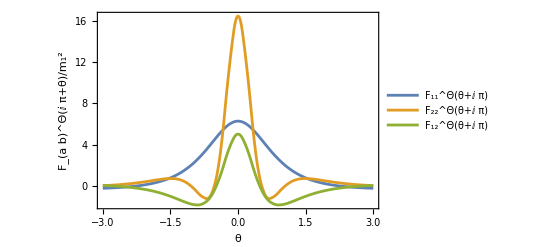

```mathematica
ListLinePlot[
{
dataFInOut11,
dataFInOut22,
dataFInOut12
},
InterpolationOrder->2,
PlotRange->All,
PlotLegends->{
(Subscript[F, 11]^Θ)[θ+ⅈ π],(Subscript[F, 22]^Θ)[θ+ⅈ π],(Subscript[F, 12]^Θ)[θ+ⅈ π]
},
LabelStyle->{Black,FontFamily->"Times New Roman",FontSize->16},
Frame->True,
FrameStyle->Black,
FrameLabel->{θ,Row[{(Subscript[F, a b]^Θ)[θ+ⅈ π],"/",Subscript[m, 1]^2}]}
]
```

```mathematica
(*dataFInOut11More=Monitor[Table[
{xx,fSigDirect[100,100][1,1,ⅈ π+xx]},
{xx,Replace[Subdivide[0,3,100],0->1/10000,1]}
],xx//N];*)
```

```mathematica
(*dataFInOut22More=Monitor[Table[
{xx,fSigDirect[100,100][2,2,ⅈ π+xx]},
{xx,Replace[Subdivide[0,3,100],0->1/10000,1]}
],xx//N];*)
```

```mathematica
(*dataFInOut11Interpolation=Interpolation[dataFInOut11More,InterpolationOrder->2]*)
```

InterpolatingFunction[…]

```mathematica
dataFInOut11Interpolation=InterpolatingFunction[…];
```

```mathematica
(*dataFInOut22Interpolation=Interpolation[dataFInOut22More,InterpolationOrder->2]*)
```

InterpolatingFunction[…]

```mathematica
dataFInOut22Interpolation=InterpolatingFunction[…];
```

```mathematica
(*dataFInOut33More=Monitor[Table[
{xx,fSigDirect[100,100][3,3,ⅈ π+xx]},
{xx,Replace[Subdivide[0,3,100],0->1/10000,1]}
],xx//N];*)
```

```mathematica
(*dataFInOut33Interpolation=Interpolation[dataFInOut33More,InterpolationOrder->2]*)
```

```mathematica
dataFInOut33Interpolation=InterpolatingFunction[…];
```

InterpolatingFunction::dmval: Input value {0} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

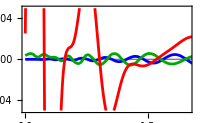

```mathematica
pltFormFactorsInOutRelative=ListPlot[
{
{#[[1]],#[[2]]-dataFInOut11Interpolation[#[[1]]]}&/@dataFormFactorLCTInOut11,
{#[[1]],#[[2]]-dataFInOut22Interpolation[#[[1]]]}&/@dataFormFactorLCTInOut22,
{#[[1]],#[[2]]-dataFInOut33Interpolation[#[[1]]]}&/@dataFormFactorLCTInOut33
},
Joined->True,
PlotRange->{{0,2},{-0.05,0.05}},
PlotStyle->{
Directive[Blue], 
Directive[Green//Darker], 
Directive[Red]
},
InterpolationOrder->2,
LabelStyle->{Black,FontFamily->"Times New Roman",FontSize->12},
Frame->True,
FrameStyle->Black,
ImageSize->200,
Prolog->{
Gray,Line[{{0,0},{4,0}}]
}
]
```

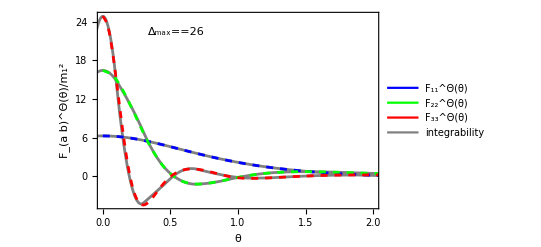

```mathematica
ListLinePlot[
{
dataFInOut11,
dataFInOut22,
dataFInOut33,
dataFormFactorLCTInOut11,
dataFormFactorLCTInOut22,
dataFormFactorLCTInOut33
},
PlotStyle->{
Gray,Gray,Gray,
Directive[Dashed,Blue], 
Directive[Dashed,Green], 
Directive[Dashed,Red]
},
InterpolationOrder->2,
PlotRange->{{0,2},All},
LabelStyle->{Black,FontFamily->"Times New Roman",FontSize->16},
Frame->True,
FrameStyle->Black,
FrameLabel->{θ,Row[{(Subscript[F, a b]^Θ)[θ],"/",Subscript[m, 1]^2}]},
Epilog->{
Inset[ 
LineLegend[
{Directive[Blue], 
Directive[Green], 
Directive[Red],Gray},
{
(Subscript[F, 11]^Θ)[θ],(Subscript[F, 22]^Θ)[θ],(Subscript[F, 33]^Θ)[θ],"integrability"
},
LabelStyle->{Black,FontFamily->"Times New Roman",FontSize->12}
],
Scaled[{.32,.6}]
],
Inset[
pltFormFactorsInOutRelative,
Scaled[{.7,.7}]
],
Black,FontFamily->"Times New Roman",FontSize->12,
Text[Subscript[Δ, max]==26,Scaled[{.28,.9}]]
},
ImageSize->400
]
```

## Run

```mathematica
ClearAll[computeLCTWithEvecs]
computeLCTWithEvecs[m_,dmax_]:=computeLCTWithEvecs[m,dmax]=Module[
{idx,evals,evecs,mp,g=1},
idx=Select[dictionary,#[[1]]/2+#[[2]]<=dmax&]//Keys;
mp=m/√((-sigmaEtaFit[m]2π (*m^(1/8)*))/16)//N;
(*mp//Print;Abort[];*)
{evals,evecs}=Eigensystem[((-sigmaEtaFit[m]2π (*m^(1/8)*))/16 sigmaMatD36+(m^2 massMatsD36["massFinite"]+(2Log[dmax] m^2+If[mp>=8,100 m^2,fct[mp] m^2])massMatsD36["massSingular"]))[[idx,idx]]
]//Transpose//SortBy[First]//Transpose;
<|"m"->m,"μVec"->√evals,"cVec"->Abs[evecs[[;;,1]]]^2/2,
"evecs"->evecs[[;;10]]
|>
]
```

```mathematica
dataFormFactorLCTEta4NN=Module[
{(*idx=3,*)m=4,evec,mRatio,data},
Monitor[Table[
data=computeLCTWithEvecs[m,26];
evec=data["evecs"][[idx]];
mRatio=(data["μVec"][[idx]])/(data["μVec"][[1]]);
Table[
{θ,2π mRatio^2 evec.(Outer[
FFactorsMemoized[#1,#2,Cosh[θ]-Sinh[θ]]&,
#[[1]]/2+#[[2]]&/@dictionaryD26//Values,
#[[1]]/2+#[[2]]&/@dictionaryD26//Values
]*tmmMatD26).evec},
{θ,Subdivide[0,3,80]}
],
{idx,1,10}
],idx]
];
```

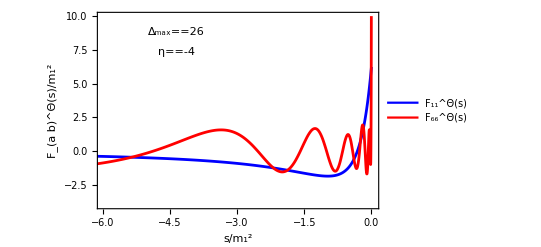

```mathematica
pltFormFactorLCTEta4NN=ListPlot[
MapAt[2(1-Cosh[#])&,
dataFormFactorLCTEta4NN,
{All,All,1}][[{1,6},2;;]],
PlotRange->{{-6,0.04},{-4,10}},
Joined->True,
InterpolationOrder->2,
PlotStyle->{Blue,Red},
LabelStyle->{Black,FontFamily->"Times New Roman",FontSize->16},
Frame->True,
FrameStyle->Black,
FrameLabel->{Row[{s,"/",Subscript[m, 1]^2}],Row[{(Subscript[F, a b]^Θ)[s],"/",Subscript[m, 1]^2}]},
Epilog->{
Inset[ 
LineLegend[
{Directive[Blue],  
Directive[Red]},
{
(Subscript[F, 11]^Θ)[s],(Subscript[F, 66]^Θ)[s]
},
LabelStyle->{Black,FontFamily->"Times New Roman",FontSize->12}
],
Scaled[{.28,.6}]
],
Black,FontFamily->"Times New Roman",FontSize->12,
Text[Subscript[Δ, max]==26,Scaled[{.28,.9}]],
Text[η==-4,Scaled[{.28,.8}]]
}
]
```

```mathematica
dataFormFactorLCTEta1NN=Module[
{(*idx=3,*)m=1,evec,mRatio,data},
Monitor[Table[
data=computeLCTWithEvecs[m,26];
evec=data["evecs"][[idx]];
mRatio=(data["μVec"][[idx]])/(data["μVec"][[1]]);
Table[
{θ,2π mRatio^2 evec.(Outer[
FFactorsMemoized[#1,#2,Cosh[θ]-Sinh[θ]]&,
#[[1]]/2+#[[2]]&/@dictionaryD26//Values,
#[[1]]/2+#[[2]]&/@dictionaryD26//Values
]*tmmMatD26).evec},
{θ,Subdivide[0,3,80]}
],
{idx,1,3}
],idx]
];
```

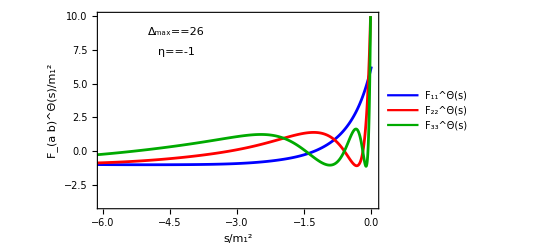

```mathematica
pltFormFactorLCTEta1NN=ListPlot[
MapAt[2(1-Cosh[#])&,
dataFormFactorLCTEta1NN,
{All,All,1}][[{1,2,3},2;;]],
PlotRange->{{-6,0.04},{-4,10}},
Joined->True,
InterpolationOrder->2,
PlotStyle->{Blue,Red,Darker@Green},
LabelStyle->{Black,FontFamily->"Times New Roman",FontSize->16},
Frame->True,
FrameStyle->Black,
FrameLabel->{Row[{s,"/",Subscript[m, 1]^2}],Row[{(Subscript[F, a b]^Θ)[s],"/",Subscript[m, 1]^2}]},
Epilog->{
Inset[ 
LineLegend[
{Directive[Blue],  
Directive[Red],
Directive[Darker@Green]
},
{
(Subscript[F, 11]^Θ)[s],(Subscript[F, 22]^Θ)[s],(Subscript[F, 33]^Θ)[s]
},
LabelStyle->{Black,FontFamily->"Times New Roman",FontSize->12}
],
Scaled[{.28,.54}]
],
Black,FontFamily->"Times New Roman",FontSize->12,
Text[Subscript[Δ, max]==26,Scaled[{.28,.9}]],
Text[η==-1,Scaled[{.28,.8}]]
}
]
```

```mathematica
ClearAll[computePadeFitFormFactorsSigma]
computePadeFitFormFactorsSigma[idx_]:=computePadeFitFormFactorsSigma[idx]=Module[
{evec,mRatio,data,wFunc,wnCoe,myPade},
data=computeLCTSigmaWithEvecs[26];
evec=data["evecs"][[idx]];
mRatio=(data["μVec"][[idx]])/(data["μVec"][[1]]);
wFunc=2π mRatio^2 evec.(Outer[
FFactorsMemoized[#1,#2,(1-(w+1/w)/2)/2]&,
#[[1]]/2+#[[2]]&/@dictionaryD26//Values,
#[[1]]/2+#[[2]]&/@dictionaryD26//Values
]*tmmMatD26).evec;
wnCoe=(SeriesCoefficient[wFunc//Expand,{w,0,#}]/(1+KroneckerDelta[#,0])&/@Range[0,20]);
myPade=PadeApproximant[wnCoe.(w^#&/@Range[0,20])/.w->(4ρ)/(1+ρ)^2,{ρ,0,{8,8}}]/.ρ->(2-2 √(1-w)-w)/w;
Function[X,
(myPade/.w-> 1-2 X-2 √(-X+X^2))+(myPade/.w-> 1-2 X+2 √(-X+X^2))//Evaluate
]
]
```

```mathematica
formFactorFitSigma1=computePadeFitFormFactorsSigma[1];
formFactorFitSigma2=computePadeFitFormFactorsSigma[2];
formFactorFitSigma3=computePadeFitFormFactorsSigma[3];
```

```mathematica
dataFInOut11Interpolation=InterpolatingFunction[…];
```

```mathematica
dataFInOut22Interpolation=InterpolatingFunction[…];
```

```mathematica
dataFInOut33Interpolation=InterpolatingFunction[…];
```

InterpolatingFunction::dmval: Input value {0} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

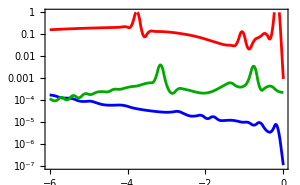

```mathematica
pltFormFactorsInInRelative=ListLogPlot[
{
Table[
{s,Abs[formFactorFitSigma1[1/2 (2+√(-4+s) √s-s)]/dataFInOut11Interpolation[ArcCosh[1-s/2]]-1]},
{s,Subdivide[-6,0,40]}
],
Table[
{s*E8Spectrum[[2]]^2,Abs[formFactorFitSigma2[1/2 (2+√(-4+s) √s-s)]/dataFInOut22Interpolation[ArcCosh[1-s/2]]-1]},
{s,Subdivide[-6/E8Spectrum[[2]]^2,0,40]}
],
Table[
{s*E8Spectrum[[3]]^2,Abs[formFactorFitSigma3[1/2 (2+√(-4+s) √s-s)]/dataFInOut33Interpolation[ArcCosh[1-s/2]]-1]},
{s,Subdivide[-6/E8Spectrum[[3]]^2,0,40]}
]
},
Joined->True,
InterpolationOrder->2,
PlotRange->{All,{10^-7,1}},
PlotStyle->{
Directive[Blue], 
Directive[Green//Darker], 
Directive[Red]
},

LabelStyle->{Black,FontFamily->"Times New Roman",FontSize->12},
Frame->True,
FrameStyle->Black,
ImageSize->300
]
```

InterpolatingFunction::dmval: Input value {0} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

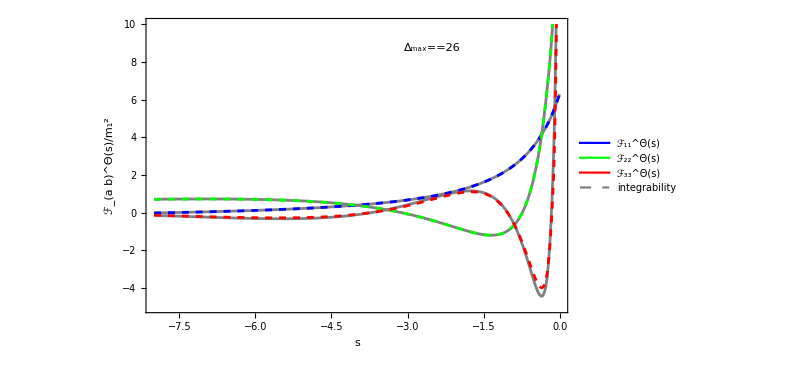

```mathematica
pltFormFactorsSigma=ListPlot[
{
Table[
{s,formFactorFitSigma1[1/2 (2+√(-4+s) √s-s)]//Re},
{s,Subdivide[-8,0,60]}
],
Table[
{s*E8Spectrum[[2]]^2,formFactorFitSigma2[1/2 (2+√(-4+s) √s-s)]//Re},
{s,Subdivide[-8/E8Spectrum[[2]]^2,0,60]}
],
Table[
{s*E8Spectrum[[3]]^2,formFactorFitSigma3[1/2 (2+√(-4+s) √s-s)]//Re},
{s,Subdivide[-8/E8Spectrum[[3]]^2,0,100]}
],
Table[
{s,dataFInOut11Interpolation[ArcCosh[1-s/2]]//Re},
{s,Subdivide[-8,0,60]}
],
Table[
{s*E8Spectrum[[2]]^2,dataFInOut22Interpolation[ArcCosh[1-s/2]]//Re},
{s,Subdivide[-8/E8Spectrum[[2]]^2,0,60]}
],
Table[
{s*E8Spectrum[[3]]^2,dataFInOut33Interpolation[ArcCosh[1-s/2]]//Re},
{s,Subdivide[-8/E8Spectrum[[3]]^2,0,100]}
]
},
Joined->True,
InterpolationOrder->2,
PlotRange->{All,{-5,10}},
PlotStyle->{
Gray,Gray,Gray,
Directive[Dashed,Blue], 
Directive[Dashed,Green], 
Directive[Dashed,Red]
},
InterpolationOrder->2,
LabelStyle->{Black,FontFamily->"Times New Roman",FontSize->16},
Frame->True,
FrameStyle->Black,
FrameLabel->{s,Row[{(Subscript[ℱ, a b]^Θ)[s],"/",Subscript[m, 1]^2}]},
Epilog->{
Inset[ 
LineLegend[
{Directive[Blue], 
Directive[Green], 
Directive[Red],Directive[Gray,Dashed]},
{
(Subscript[ℱ, 11]^Θ)[s],(Subscript[ℱ, 22]^Θ)[s],(Subscript[ℱ, 33]^Θ)[s],"integrability"
},
LabelStyle->{Black,FontFamily->"Times New Roman",FontSize->18},
LegendLayout->"Row"
],
Scaled[{.32,.18}]
],
Inset[
pltFormFactorsInOutRelative,
Scaled[{.3,.7}]
],
Black,FontFamily->"Times New Roman",FontSize->18,
Text[Subscript[Δ, max]==26,Scaled[{.68,.9}]]
},
ImageSize->600
]
```

## Off diagonal

```mathematica
ClearAll[FFactorsMemoized2]
FFactorsMemoized2[h1_,h2_,m1_,m2_,X_]:=FFactorsMemoized2[h1,h2,m1,m2,X]=With[{hO=2},
(-(m1 m2 (-1+X))/(m1^2-m2^2 X))^-1(m1/m2)^(-(hO/2-h1))(m1/(m2 X))^(1/2 (-2 h1+hO))RegJacobiP[-1-h1+h2+hO,-1+2 h1,1-2 hO,1-2 X]
];
```

```mathematica
ClearAll[computePadeFitFormFactorsSigmaOffDiag2]
computePadeFitFormFactorsSigmaOffDiag2[idx1_,idx2_]:=computePadeFitFormFactorsSigmaOffDiag2[idx1,idx2]=Module[
{evec1,evec2,m1,m2,data,wFunc,wnCoe,myPade},
data=computeLCTSigmaWithEvecs[26];
evec1=data["evecs"][[idx1]];
evec2=data["evecs"][[idx2]];
m1=(data["μVec"][[idx1]])/(data["μVec"][[1]]);
m2=(data["μVec"][[idx2]])/(data["μVec"][[1]]);
wFunc=2π m1 m2 evec1.(Outer[
FFactorsMemoized2[#1,#2,m1,m2,(1-(w+1/w)/2)/2]&,
#[[1]]/2+#[[2]]&/@dictionaryD26//Values,
#[[1]]/2+#[[2]]&/@dictionaryD26//Values
]*tmmMatD26).evec2;
wnCoe=(SeriesCoefficient[wFunc//Expand,{w,0,#}]/(1+KroneckerDelta[#,0])&/@Range[0,20]);
myPade=PadeApproximant[wnCoe.(w^#&/@Range[0,20])/.w->(4ρ)/(1+ρ)^2,{ρ,0,{8,8}}]/.ρ->(2-2 √(1-w)-w)/w;
Function[X,
(myPade/.w-> 1-2 X-2 √(-X+X^2))+(myPade/.w-> 1-2 X-2 √(-X+X^2))//Evaluate
]
]
```

```mathematica
formFactorFitSigma12=computePadeFitFormFactorsSigmaOffDiag2[1,2];
```

```mathematica
formFactorFitSigma13=computePadeFitFormFactorsSigmaOffDiag2[1,3];
```

```mathematica
formFactorFitSigma23=computePadeFitFormFactorsSigmaOffDiag2[2,3];
```

```mathematica
(*dataFInOut12More=Monitor[Table[
{xx,fSigDirect[100,100][1,2,ⅈ π+xx]},
{xx,Replace[Subdivide[0,3,100],0->1/10000,1]}
],xx//N];*)
```

```mathematica
(*dataFInOut13More=Monitor[Table[
{xx,fSigDirect[100,100][1,3,ⅈ π+xx]},
{xx,Replace[Subdivide[0,3,100],0->1/10000,1]}
],xx//N];*)
```

```mathematica
(*dataFInOut12Interpolation=Interpolation[dataFInOut12More,InterpolationOrder->2]*)
```

InterpolatingFunction[…]

```mathematica
dataFInOut12Interpolation=InterpolatingFunction[…];
```

```mathematica
(*dataFInOut13Interpolation=Interpolation[dataFInOut13More,InterpolationOrder->2]*)
```

InterpolatingFunction[…]

```mathematica
dataFInOut13Interpolation=InterpolatingFunction[…];
```

```mathematica
(*dataFInOut23More=Monitor[Table[
{xx,fSigDirect[100,100][2,3,ⅈ π+xx]},
{xx,Replace[Subdivide[0,3,100],0->1/10000,1]}
],xx//N];*)
```

```mathematica
(*dataFInOut23Interpolation=Interpolation[dataFInOut23More,InterpolationOrder->2]*)
```

InterpolatingFunction[…]

```mathematica
dataFInOut23Interpolation=InterpolatingFunction[…];
```

InterpolatingFunction::dmval: Input value {0} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

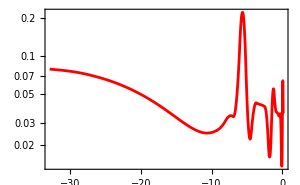

```mathematica
pltFormFactorsOffDiagInOutRelative=Block[
{m1=E8Spectrum[[1]],m2=E8Spectrum[[2]],m3=E8Spectrum[[3]]},
ListLogPlot[
{
Table[
{m1^2+m2^2-2m1 m2 Cosh[θ],Abs[(formFactorFitSigma12[m1/m2 ⅇ^-θ]//Re)/dataFInOut12Interpolation[θ]-1]},
{θ,Subdivide[0,3,30]}
],
Table[
{m1^2+m3^2-2m1 m3 Cosh[θ],Abs[(formFactorFitSigma13[m1/m3 ⅇ^-θ]//Re)/dataFInOut13Interpolation[θ]-1]},
{θ,Subdivide[0,3,30]}
],
Table[
{m2^2+m3^2-2m2 m3 Cosh[θ],Abs[(formFactorFitSigma23[m2/m3 ⅇ^-θ]//Re)/dataFInOut23Interpolation[θ]-1]},
{θ,Subdivide[0,2.5,30]}
]
},
Joined->True,
InterpolationOrder->2,
PlotRange->{{-30,All},{10^-7,1}},
PlotStyle->{
Directive[Blue], 
Directive[Green//Darker], 
Directive[Red]
},

LabelStyle->{Black,FontFamily->"Times New Roman",FontSize->12},
Frame->True,
FrameStyle->Black,
ImageSize->300
]
]
```

InterpolatingFunction::dmval: Input value {0} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

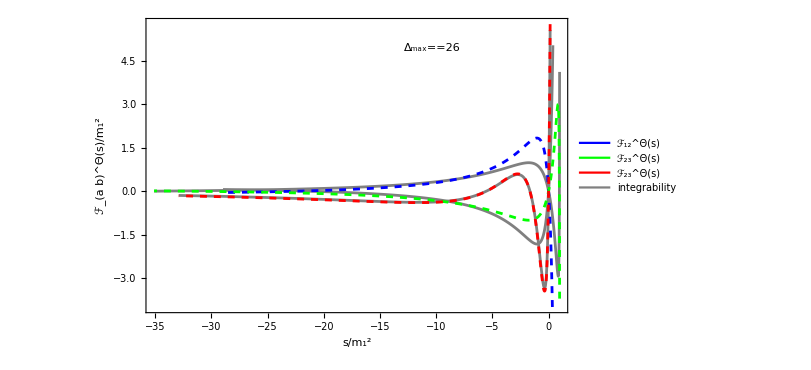

```mathematica
pltFormFactorsSigmaOffDiag=Block[
{m1=E8Spectrum[[1]],m2=E8Spectrum[[2]],m3=E8Spectrum[[3]]},
ListPlot[
{
Table[
{m1^2+m2^2-2m1 m2 Cosh[θ],dataFInOut12Interpolation[θ]},
{θ,Subdivide[0,3,30]}
],
Table[
{m1^2+m3^2-2m1 m3 Cosh[θ],dataFInOut13Interpolation[θ]},
{θ,Subdivide[0,3,30]}
],
Table[
{m2^2+m3^2-2m2 m3 Cosh[θ],dataFInOut23Interpolation[θ]},
{θ,Subdivide[0,2.5,30]}
]
,
Table[
{m1^2+m2^2-2m1 m2 Cosh[θ],formFactorFitSigma12[m1/m2 ⅇ^-θ]//Re},
{θ,Subdivide[0,3,30]}
],
Table[
{m1^2+m3^2-2m1 m3 Cosh[θ],formFactorFitSigma13[m1/m3 ⅇ^-θ]//Re},
{θ,Subdivide[0,3,30]}
],
Table[
{m2^2+m3^2-2m2 m3 Cosh[θ],formFactorFitSigma23[m2/m3 ⅇ^-θ]//Re},
{θ,Subdivide[0,2.5,30]}
]
},
Joined->True,
InterpolationOrder->2,
PlotRange->{{-30,All},{-4,6}},
PlotStyle->{
Gray,Gray,Gray,
Directive[Dashed,Blue], 
Directive[Dashed,Green], 
Directive[Dashed,Red]
},
InterpolationOrder->2,
LabelStyle->{Black,FontFamily->"Times New Roman",FontSize->16},
Frame->True,
FrameStyle->Black,
PlotRange->{{-30,All},Automatic},
FrameLabel->{Row[{s,"/",Subscript[m, 1]^2}],Row[{(Subscript[ℱ, a b]^Θ)[s],"/",Subscript[m, 1]^2}]},
Epilog->{
Inset[ 
LineLegend[
{Directive[Blue], 
Directive[Green], 
Directive[Red],Gray},
{
(Subscript[ℱ, 12]^Θ)[s],(Subscript[ℱ, 23]^Θ)[s],(Subscript[ℱ, 23]^Θ)[s],"integrability"
},
LabelStyle->{Black,FontFamily->"Times New Roman",FontSize->18},
LegendLayout->"Row"
],
Scaled[{.32,.18}]
],
Inset[
pltFormFactorsOffDiagInOutRelative,
Scaled[{.3,.7}]
],
Black,FontFamily->"Times New Roman",FontSize->18,
Text[Subscript[Δ, max]==26,Scaled[{.68,.9}]]
},
ImageSize->600
]
]
```